```mathematica
ClearAll["Global`*"]
Quit
```

```mathematica
m=5;
```

Create a m x m central difference matrix

```mathematica
A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;
A //MatrixForm
(* ν = a k/h *)
```

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

Check if there exists a value ν =  a k/h > 0 such that entries of (I - (νA))^-1 are positive. 
The following checks if each off-diagonal entries of  (I - (νA))^-1 can be positive for certain values of ν.
If False is returned, then that means that there is at least a negative off-diagonal entry in  (I + (νA))^-1 for any ν>0

```mathematica
BE = Inverse[IdentityMatrix[Length[A]]-ν A];
listall = Table[Reduce[{BE[[i,j]]≥ 0,ν≠0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{BE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
Reduce[DeleteDuplicates[Join@@listall]]//N
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//N
```

ν≤-4.41114||ν≥4.41114

{ν>0.,ν≥4.41114}

```mathematica
BE//MatrixForm
```

((1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16))

```mathematica
ν=Root[-8-6 #1^2+#1^3&,1]
DeleteDuplicates[Join@@Table[BE[[i,j]],{i,1,m},{j,1,m}]]//Simplify//N
```

Root[-8-6 #1^2+#1^3&,1]

{0.177815,0.212994,0.109191,0.177815,0.0519017,0.161093,0.,0.161093,-0.0519017}

```mathematica
BE = Inverse[IdentityMatrix[Length[A]]-ν A];
listall = Table[Reduce[{BE[[i,j]]≥ 0, ν ≠0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{BE[[i,j]]≥ 0,ν ≠0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//N
```

{ν<0||ν>0,ν≤Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]||ν>0,ν≤Root[8+6 #1^2+#1^3&,1]||ν>0,ν<0||ν≥Root[-8-6 #1^2+#1^3&,1],ν<0||ν≥Root[-128-192 #1^2-80 #1^4-8 #1^6+#1^7&,1]}

{ν≤-9.01393||ν>0.,ν<0.||ν>0.,ν≤-6.20761||ν>0.,ν<0.||ν≥6.20761,ν<0.||ν≥9.01393}

Non-repeated off-diagonal entries of (I - (νA))^-1:

```mathematica
DeleteCases[DeleteDuplicates[Join@@Table[If[i≠ j,BE[[i,j]]],{i,1,m},{j,1,m}]],Null]//Simplify
```

{(ν (128+192 ν^2+80 ν^4+8 ν^6+ν^7))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^2 (64+80 ν^2+24 ν^4-2 ν^5+ν^6))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^3 (32+32 ν^2+4 ν^3+6 ν^4+ν^5))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^4 (16-8 ν+12 ν^2-4 ν^3+ν^4))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^4 (16+8 ν+12 ν^2+4 ν^3+ν^4))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^3 (-32-32 ν^2+4 ν^3-6 ν^4+ν^5))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^2 (64+80 ν^2+24 ν^4+2 ν^5+ν^6))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν (-128-192 ν^2-80 ν^4-8 ν^6+ν^7))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8)}

One can see that if m is even, then there exists a negative entry in (I + (νA))^-1 for ν > 0.
But if m is odd, then we can obtain a lower bound on ν such that all off-diagonal entries are positive. If some matrix entries have numerators that attain negative values, then admissible values of ν for positivity depend on roots of the numerator.

```mathematica
ν=Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]
DeleteCases[DeleteDuplicates[Join@@Table[BE[[i,j]],{i,1,m},{j,1,m}]],Null]//Simplify//N
```

Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]

{0.145067,0.,0.145067,0.0321872,0.152208,0.065959,0.166843,0.102978,0.189692}

Check the same in the case of explicit Euler, i.e positivity of I-νA. Obviously this is not true for any value of m.

```mathematica
FE = IdentityMatrix[Length[A]]+ν A;
listall = Table[Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//Simplify
```

{ν>0,False}

{ν>0,False}

```mathematica
FE//MatrixForm
```

(1 | ν/2 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | -ν/2 | 1)

```mathematica
ClearAll["Global`*"]
Quit
```

```mathematica
m=5;
S =Table[DiagonalMatrix[ConstantArray[(-1)^(j-i+1)/2Cot[(j-1)/2 h],m-1],-1,m],{j,1,m},{i,1,m}]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];
A[[1,m]] = -1/2;
A[[m,1]] = 1/2;
A //MatrixForm
```

DiagonalMatrix::inf: Input matrix contains an infinite entry.

General::stop: Further output of DiagonalMatrix::inf will be suppressed during this calculation.

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

```mathematica
m=5;h =1/(m-1);
Table[ConstantArray[(-1)^(k-1)/2Cot[k/2 h],m-k],{k,1,m}]
```

{{1/2 Cot[1/8],1/2 Cot[1/8],1/2 Cot[1/8],1/2 Cot[1/8]},{-1/2 Cot[1/4],-1/2 Cot[1/4],-1/2 Cot[1/4]},{1/2 Cot[3/8],1/2 Cot[3/8]},{-1/2 Cot[1/2]},{}}

```mathematica
m=5;k=2;ConstantArray[(-1)^(k-1)/2Cot[k/2 h],m-k]
```

{-Cot[h]/2,-Cot[h]/2,-Cot[h]/2}

# Notation: ν vs. ν/2??? Or ν vs. (-ν), so M_(1,2)<0 vs. M_(2,1)<0?

### General θ-methods

```mathematica
m=5;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@A
```

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

```mathematica
Manipulate[Simplify@MatrixForm[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{θ,0,1,1/20}]
```

### Size=5. For θ=0:

```mathematica
Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->0]
```

{0,1,-ν/2,ν/2}

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->0]≥0]]
```

ν==0

### Size=5. For θ=1:

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->1]≥0]]
```

```mathematica
ν==0||ν≥Root[-8-4 #1^2+#1^3&,1]//N
```

ν==0.||ν≥4.41114

### Size=5. For θ=1/2:

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->1/2]≥0]]
```

ν==0

### For 0≤θ≤1:

```mathematica
m=7;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@A
```

(0 | 1/2 | 0 | 0 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | 0 | 0 | -1/2 | 0)

```mathematica
Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]//LogicalExpand
```

(θ==1&&Root[-32-32 #1^2-6 #1^4+#1^5&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-64+64 #1+12 #1^2-13 #1^3-7 #1^4+#1^5&,1]&&θ≤1&&Root[64-32 ν^2 #1+112 ν^2 #1^2-32 ν^4 #1^3+56 ν^4 #1^4-6 ν^6 #1^5+7 ν^6 #1^6&,2]≤θ)||(Root[-32-32 #1^2-6 #1^4+#1^5&,1]<ν&&θ≤1&&ν≤Root[-64+64 #1+12 #1^2-13 #1^3-7 #1^4+#1^5&,1]&&Root[-32-32 ν^2 #1^2-6 ν^4 #1^4+ν^5 #1^5&,1]≤θ)

### Conjecture: for m even and any ν>0, Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) has a negative entry.

### For odd values of m, the good (θ,ν) pairs are plotted below (= for which all entries of the matrix are non-negative). As we increase m=2k+1, the admissible region seems to shrink.

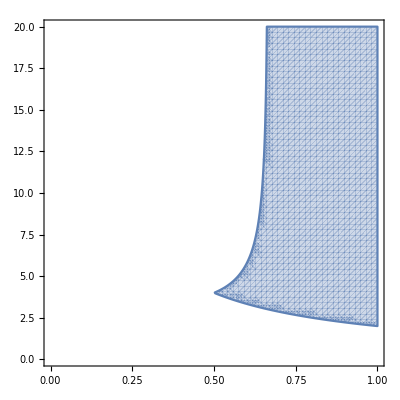

```mathematica
RegionPlot[Evaluate[m=3;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

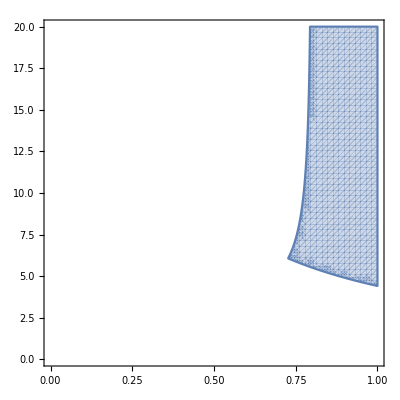

```mathematica
RegionPlot[Evaluate[m=5;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

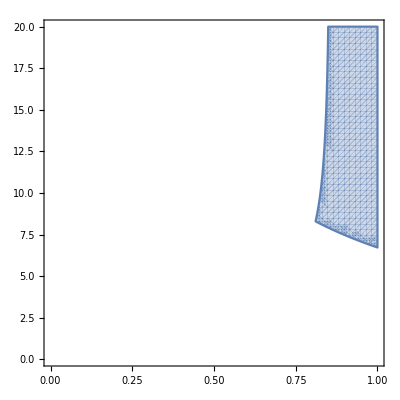

```mathematica
RegionPlot[Evaluate[m=7;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

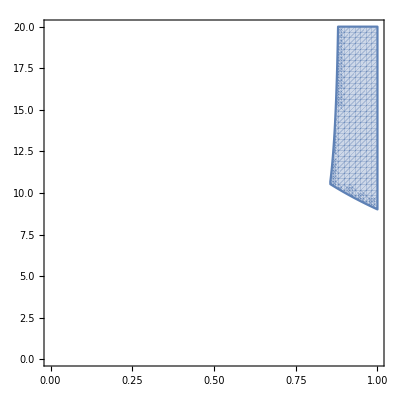

```mathematica
RegionPlot[Evaluate[m=9;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

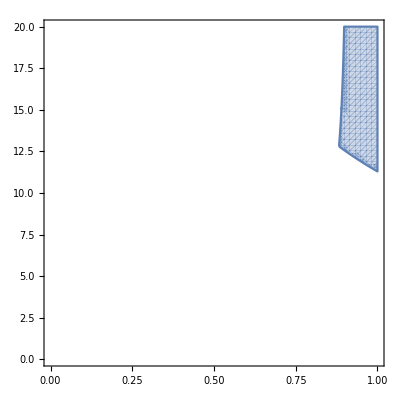

```mathematica
RegionPlot[Evaluate[m=11;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

```mathematica
Evaluate[m=13;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]]
```

(θ==1&&Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&θ≤1&&Root[4096-2048 ν^2 #1+13312 ν^2 #1^2-5120 ν^4 #1^3+16640 ν^4 #1^4-4608 ν^6 #1^5+9984 ν^6 #1^6-1792 ν^8 #1^7+2912 ν^8 #1^8-280 ν^10 #1^9+364 ν^10 #1^10-12 ν^12 #1^11+13 ν^12 #1^12&,2]≤θ)||(Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]<ν&&θ≤1&&ν≤Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&Root[-2048-5120 ν^2 #1^2-4608 ν^4 #1^4-1792 ν^6 #1^6-280 ν^8 #1^8-12 ν^10 #1^10+ν^11 #1^11&,1]≤θ)

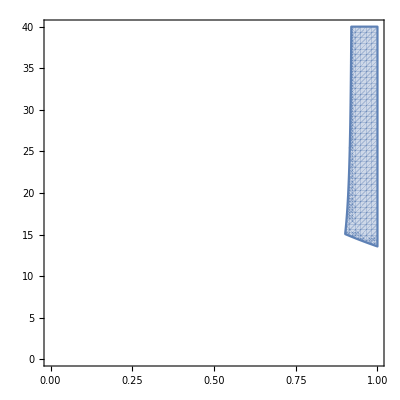

```mathematica
RegionPlot[(θ==1&&Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&θ≤1&&Root[4096-2048 ν^2 #1+13312 ν^2 #1^2-5120 ν^4 #1^3+16640 ν^4 #1^4-4608 ν^6 #1^5+9984 ν^6 #1^6-1792 ν^8 #1^7+2912 ν^8 #1^8-280 ν^10 #1^9+364 ν^10 #1^10-12 ν^12 #1^11+13 ν^12 #1^12&,2]≤θ)||(Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]<ν&&θ≤1&&ν≤Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&Root[-2048-5120 ν^2 #1^2-4608 ν^4 #1^4-1792 ν^6 #1^6-280 ν^8 #1^8-12 ν^10 #1^10+ν^11 #1^11&,1]≤θ),{θ,0,1},{ν,0,40},PlotPoints->60]
```

### Focusing on entry_(2,1) of the matrix for various odd values of m

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[2,1]],{m,3,15,2}]
```

{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-512-1024 θ^2 ν^2-672 θ^4 ν^4-160 θ^6 ν^6-10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (-2048-5120 θ^2 ν^2-4608 θ^4 ν^4-1792 θ^6 ν^6-280 θ^8 ν^8-12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (-8192-24576 θ^2 ν^2-28160 θ^4 ν^4-15360 θ^6 ν^6-4032 θ^8 ν^8-448 θ^10 ν^10-14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]
```

{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-512-1024 θ^2 ν^2-672 θ^4 ν^4-160 θ^6 ν^6-10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (-2048-5120 θ^2 ν^2-4608 θ^4 ν^4-1792 θ^6 ν^6-280 θ^8 ν^8-12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (-8192-24576 θ^2 ν^2-28160 θ^4 ν^4-15360 θ^6 ν^6-4032 θ^8 ν^8-448 θ^10 ν^10-14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,2]],{m,3,15,2}]
```

{(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (512+1024 θ^2 ν^2+672 θ^4 ν^4+160 θ^6 ν^6+10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (2048+5120 θ^2 ν^2+4608 θ^4 ν^4+1792 θ^6 ν^6+280 θ^8 ν^8+12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (8192+24576 θ^2 ν^2+28160 θ^4 ν^4+15360 θ^6 ν^6+4032 θ^8 ν^8+448 θ^10 ν^10+14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

### The θ=0 case is clear, see below. So in what follows we can assume: 0<θ≤1. Also, for ν=0, the corresponding matrix is the identity matrix, so we can assume in what follows that ν>0.

```mathematica
With[{θ=0},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,3,9,2}]]
```

{(1 | ν/2 | -ν/2
-ν/2 | 1 | ν/2
ν/2 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0
0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0
0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | 0 | 0 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ν/2 | 1)}

### Useful fact: the sum/product/inverse of circulant matrices is circulant [REFERENCE: Fact 5.16.7. in Berstein MATRIX MATHEMATICS]. Since A is circulant, the matrix Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) is circulant, too.

### These are the denominators of the first row of the θ-matrix for various odd values of m; that is, the determinant of the matrix IdentityMatrix[Length[A]]-θ ν A

```mathematica
With[{θ=θ},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Expand@Det[IdentityMatrix[Length[A]]-θ ν A],{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256,1+(11 θ^2 ν^2)/4+(11 θ^4 ν^4)/4+(77 θ^6 ν^6)/64+(55 θ^8 ν^8)/256+(11 θ^10 ν^10)/1024,1+(13 θ^2 ν^2)/4+(65 θ^4 ν^4)/16+(39 θ^6 ν^6)/16+(91 θ^8 ν^8)/128+(91 θ^10 ν^10)/1024+(13 θ^12 ν^12)/4096,1+(15 θ^2 ν^2)/4+(45 θ^4 ν^4)/8+(275 θ^6 ν^6)/64+(225 θ^8 ν^8)/128+(189 θ^10 ν^10)/512+(35 θ^12 ν^12)/1024+(15 θ^14 ν^14)/16384}

```mathematica
With[{θ=θ},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm[IdentityMatrix[Length[A]]-θ ν A],{m,3,9,2}]]
```

{(1 | -(θ ν)/2 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1)}

### Notation: μ:=(ν θ)^2>0, that is, ν→(√μ)/θ

```mathematica
{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256,1+(11 θ^2 ν^2)/4+(11 θ^4 ν^4)/4+(77 θ^6 ν^6)/64+(55 θ^8 ν^8)/256+(11 θ^10 ν^10)/1024,1+(13 θ^2 ν^2)/4+(65 θ^4 ν^4)/16+(39 θ^6 ν^6)/16+(91 θ^8 ν^8)/128+(91 θ^10 ν^10)/1024+(13 θ^12 ν^12)/4096,1+(15 θ^2 ν^2)/4+(45 θ^4 ν^4)/8+(275 θ^6 ν^6)/64+(225 θ^8 ν^8)/128+(189 θ^10 ν^10)/512+(35 θ^12 ν^12)/1024+(15 θ^14 ν^14)/16384}/.ν->(√μ)/θ
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

### The denominators of the full matrix Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) satisfy a second-order linear recurrence relation as a function of m=2k+1; we need to prove positivity for all of them for ν>0, 0<θ≤1. These denominators are the determinants of IdentityMatrix[Length[A]]-θ ν A The form of the linear recurrence must follow from recursive determinant expansions of the following kind:

```mathematica
Det[({{1, -(√μ)/2, 0, 0, 0, 0, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0}, {0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0}, {0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0}, {0, 0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, 0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, 0, 0, 0, 0, (√μ)/2, 1}})]==(1+μ/2) Det[({{1, -(√μ)/2, 0, 0, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0}, {0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, 0, 0, (√μ)/2, 1}})]-1/16 μ^2 Det[({{1, -(√μ)/2, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, (√μ)/2, 1}})]//Simplify
```

True

```mathematica
Expand@FindLinearRecurrence[{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}]
```

{1+μ/2,-μ^2/16}

### When writing down this in the manuscript, SHIFT the index by 1, so denom[1]==1+(3 μ)/4,denom[2]==1+(5 μ)/4+(5 μ^2)/16

```mathematica
RecurrenceTable[{denom[k+2]== (1+μ/2)denom[k+1]-μ^2/16 denom[k],denom[1]==1,denom[2]==1+(3 μ)/4},denom,{k,2,8}]//Expand
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
RSolve[{denom[k+2]== (1+μ/2)denom[k+1]-μ^2/16 denom[k],denom[1]==1,denom[2]==1+(3 μ)/4},denom[k],k]
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((2+μ-2 √(1+μ))^k+μ (2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k-(2+μ+2 √(1+μ))^k-μ (2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k))/(μ √(1+μ))}}//Apart//Simplify
```

{{denom[k]→-(2^(1-2 k) ((2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k-√(1+μ) (2+μ+2 √(1+μ))^k))/μ}}

Notice that 2+μ+2 √(1+μ)==(1+√(1+μ))^2 and 2+μ-2 √(1+μ)==(1-√(1+μ))^2, so

```mathematica
{{denom[k]->-(2^(1-2 k) (((1-√(1+μ))^2)^k+√(1+μ) ((1-√(1+μ))^2)^k+((1+√(1+μ))^2)^k-√(1+μ) ((1+√(1+μ))^2)^k))/μ}}//PowerExpand
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k)+√(1+μ) (1-√(1+μ))^(2 k)+(1+√(1+μ))^(2 k)-√(1+μ) (1+√(1+μ))^(2 k)))/μ}}
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k) (1+√(1+μ))-(-1+√(1+μ)) (1+√(1+μ))^(2 k)))/μ}}
```

Notice that

```mathematica
1+√(1+μ)==μ/(√(1+μ)-1)//Simplify
```

True

so

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k) (μ/(√(1+μ)-1))-(-1+√(1+μ)) (μ/(√(1+μ)-1))^(2 k)))/μ}}//PowerExpand
```

{{denom[k]→-(2^(1-2 k) ((μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))-μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}

```mathematica
{{denom[k]->(2^(1-2 k) (-(μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))+μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}
```

```mathematica
{{denom[k]->(2^(1-2 k) (-(μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))))/μ+(2^(1-2 k) (+μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}
```

```mathematica
{{denom[k]->-(2^(1-2 k) (1-√(1+μ))^(2 k))/(-1+√(1+μ))+2^(1-2 k) μ^(-1+2 k) (-1+√(1+μ))^(1-2 k)}}//Simplify
```

```mathematica
{{denom[k]->(2^(1-2 k) (-(1-√(1+μ))^(2 k)+μ^(-1+2 k) (-1+√(1+μ))^(2-2 k)))/(-1+√(1+μ))}}
```

```mathematica
{{denom[k]->2^(1-2 k)/(√(1+μ)-1) ((√(1+μ)-1)μ^(-1+2 k) (√(1+μ)-1)^(1-2 k)-(1-√(1+μ))^(2 k))}}
```

```mathematica
{{denom[k]->2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))}}
```

Check:

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->1//Simplify
```

1

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->2//Simplify
```

1+(3 μ)/4

```mathematica
(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+2)==(1+μ/2)(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+1)-μ^2/16(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1)))//Simplify
```

True

```mathematica
Table[2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))//Expand,{k,2,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+1//Simplify
```

2^(-1-2 k) (-(-1+√(1+μ))^(1+2 k)+(1+√(1+μ))^(1+2 k))

```mathematica
Table[2^(-1-2 k) (-(-1+√(1+μ))^(1+2 k)+(1+√(1+μ))^(1+2 k))//Expand,{k,1,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384,1+(17 μ)/4+(119 μ^2)/16+(221 μ^3)/32+(935 μ^4)/256+(561 μ^5)/512+(357 μ^6)/2048+(51 μ^7)/4096+(17 μ^8)/65536}

### This is the explicit form: ((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1) ; k=1 corresponds to the matrix size m=2k+1=3.

Since (√(1+μ)+1)/2>(√(1+μ)-1)/2>0, this clearly shows that all the determinants are positive, for any k≥1,1≥θ>0, ν>0, that is, with μ:=(ν θ )^2>0.

```mathematica
Table[((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1)//Expand,{k,1,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384,1+(17 μ)/4+(119 μ^2)/16+(221 μ^3)/32+(935 μ^4)/256+(561 μ^5)/512+(357 μ^6)/2048+(51 μ^7)/4096+(17 μ^8)/65536}

### Similarly, there seems to be just two kinds of recurrences as a function of m=2k+1 for the polynomials in the numerators (but with different starting values)

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,15,2}]
```

{2 (2+θ^2 ν^2),-θ^4 ν^4}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,2]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[2,1]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,3]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,4]],{m,5,17,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,3,5,2}]
```

{{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2)},{(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2),(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2)}},{{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4)}}}

### Just considering the 1st row of some matrices for different odd values of m:

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]
```

{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(64-32 θ ν^2+112 θ^2 ν^2-32 θ^3 ν^4+56 θ^4 ν^4-6 θ^5 ν^6+7 θ^6 ν^6)/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2-2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (8+4 θ ν+4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (-8+4 θ ν-4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2+2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)},{(256-128 θ ν^2+576 θ^2 ν^2-192 θ^3 ν^4+432 θ^4 ν^4-80 θ^5 ν^6+120 θ^6 ν^6-8 θ^7 ν^8+9 θ^8 ν^8)/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4-2 θ^5 ν^5+θ^6 ν^6))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^2 ν^3 (32+32 θ^2 ν^2+4 θ^3 ν^3+6 θ^4 ν^4+θ^5 ν^5))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^3 ν^4 (16-8 θ ν+12 θ^2 ν^2-4 θ^3 ν^3+θ^4 ν^4))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^3 ν^4 (16+8 θ ν+12 θ^2 ν^2+4 θ^3 ν^3+θ^4 ν^4))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^2 ν^3 (-32-32 θ^2 ν^2+4 θ^3 ν^3-6 θ^4 ν^4+θ^5 ν^5))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4+2 θ^5 ν^5+θ^6 ν^6))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8)}}

# Focusing on the θ=1/2 special case: we get the “negative” result by comparing the numerators of the first and last entries of the first row of the matrix of odd size (assuming that the denominators are positive).

```mathematica
With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9}]]
```

{{(16-ν^2)/(16+3 ν^2),(2 ν (4+ν))/(16+3 ν^2),(2 (-4+ν) ν)/(16+3 ν^2)},{4/(4+ν^2),(2 ν)/(4+ν^2),ν^2/(4+ν^2),-(2 ν)/(4+ν^2)},{(256+16 ν^2-3 ν^4)/(256+80 ν^2+5 ν^4),(2 ν (64+8 ν^2+ν^3))/(256+80 ν^2+5 ν^4),(2 ν^2 (16-4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν^2 (16+4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν (-64-8 ν^2+ν^3))/(256+80 ν^2+5 ν^4)},{(16-ν^2)/(16+3 ν^2),(8 ν)/(16+3 ν^2),(2 ν^2)/(16+3 ν^2),0,(2 ν^2)/(16+3 ν^2),-(8 ν)/(16+3 ν^2)},{(4096+768 ν^2-32 ν^4-5 ν^6)/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (1024+256 ν^2+12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2-4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (64+16 ν+8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (-64+16 ν-8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2+4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (-1024-256 ν^2-12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6)},{(64+8 ν^2-ν^4)/(64+24 ν^2+2 ν^4),(ν (16+3 ν^2))/(32+12 ν^2+ν^4),ν^2/(8+2 ν^2),ν^3/(32+12 ν^2+ν^4),ν^4/(64+24 ν^2+2 ν^4),-ν^3/(32+12 ν^2+ν^4),ν^2/(8+2 ν^2),-(ν (16+3 ν^2))/(32+12 ν^2+ν^4)},{(65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8)/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8)}}

```mathematica
With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{(16-ν^2)/(16+3 ν^2),(2 ν (4+ν))/(16+3 ν^2),(2 (-4+ν) ν)/(16+3 ν^2)},{(256+16 ν^2-3 ν^4)/(256+80 ν^2+5 ν^4),(2 ν (64+8 ν^2+ν^3))/(256+80 ν^2+5 ν^4),(2 ν^2 (16-4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν^2 (16+4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν (-64-8 ν^2+ν^3))/(256+80 ν^2+5 ν^4)},{(4096+768 ν^2-32 ν^4-5 ν^6)/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (1024+256 ν^2+12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2-4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (64+16 ν+8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (-64+16 ν-8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2+4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (-1024-256 ν^2-12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6)},{(65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8)/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8)}}

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{16-ν^2,2 ν (4+ν),2 (-4+ν) ν},{256+16 ν^2-3 ν^4,2 ν (64+8 ν^2+ν^3),2 ν^2 (16-4 ν+ν^2),2 ν^2 (16+4 ν+ν^2),2 ν (-64-8 ν^2+ν^3)},{4096+768 ν^2-32 ν^4-5 ν^6,2 ν (1024+256 ν^2+12 ν^4+ν^5),2 ν^2 (256+48 ν^2-4 ν^3+ν^4),2 ν^3 (64+16 ν+8 ν^2+ν^3),2 ν^3 (-64+16 ν-8 ν^2+ν^3),2 ν^2 (256+48 ν^2+4 ν^3+ν^4),2 ν (-1024-256 ν^2-12 ν^4+ν^5)},{65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7),2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6),2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5),2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4),2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4),2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5),2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7)}}

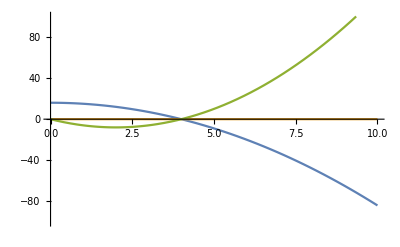

```mathematica
Plot[{16-ν^2,0 2 ν (4+ν),2 (-4+ν) ν},{ν,0,10},PlotRange->{-100,100}]
```

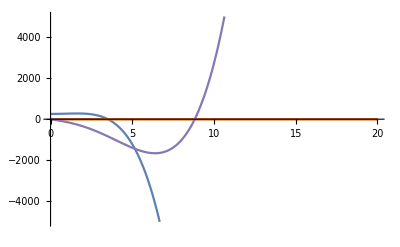

```mathematica
Plot[{256+16 ν^2-3 ν^4,0 2 ν (64+8 ν^2+ν^3),0 2 ν^2 (16-4 ν+ν^2),0 2 ν^2 (16+4 ν+ν^2),2 ν (-64-8 ν^2+ν^3)},{ν,0,20},PlotRange->{-5000,5000}]
```

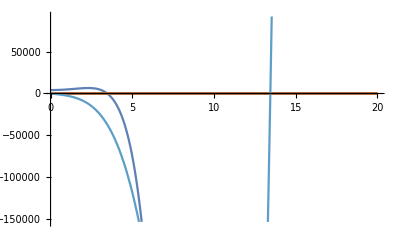

```mathematica
Plot[{4096+768 ν^2-32 ν^4-5 ν^6,0 2 ν (1024+256 ν^2+12 ν^4+ν^5),0 2 ν^2 (256+48 ν^2-4 ν^3+ν^4),0 2 ν^3 (64+16 ν+8 ν^2+ν^3),0 2 ν^3 (-64+16 ν-8 ν^2+ν^3), 0 2 ν^2 (256+48 ν^2+4 ν^3+ν^4),2 ν (-1024-256 ν^2-12 ν^4+ν^5)},{ν,0,20}]
```

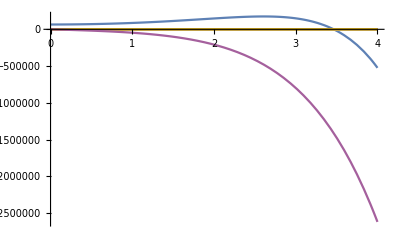

```mathematica
Plot[{65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,0 2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7),0 2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6),0 2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5),0 2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4),0 2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4),0 2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5),0 2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7)},{ν,0,4}]
```

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,17,2}]]
```

{16-ν^2,256+16 ν^2-3 ν^4,4096+768 ν^2-32 ν^4-5 ν^6,65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,1048576+458752 ν^2+49152 ν^4-1792 ν^6-400 ν^8-9 ν^10,16777216+9437184 ν^2+1638400 ν^4+49152 ν^6-10752 ν^8-784 ν^10-11 ν^12,268435456+184549376 ν^2+44040192 ν^4+3604480 ν^6-122880 ν^8-32256 ν^10-1344 ν^12-13 ν^14,4294967296+3489660928 ν^2+1056964608 ν^4+136314880 ν^6+3604480 ν^8-811008 ν^10-75264 ν^12-2112 ν^14-15 ν^16}

```mathematica
FindLinearRecurrence[Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,15,2}]]]
```

{2 (8+ν^2),-ν^4}

```mathematica
RSolve[{topleftpoly[n+2]==2 (8+ν^2)topleftpoly[n+1]-ν^4  topleftpoly[n],topleftpoly[0]==1,topleftpoly[1]==16-ν^2 },topleftpoly[n],n]
```

{{topleftpoly[n]→(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))}}

```mathematica
Table[(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))//Simplify,{n,1,8}]
```

{16-ν^2,256+16 ν^2-3 ν^4,4096+768 ν^2-32 ν^4-5 ν^6,65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,1048576+458752 ν^2+49152 ν^4-1792 ν^6-400 ν^8-9 ν^10,16777216+9437184 ν^2+1638400 ν^4+49152 ν^6-10752 ν^8-784 ν^10-11 ν^12,268435456+184549376 ν^2+44040192 ν^4+3604480 ν^6-122880 ν^8-32256 ν^10-1344 ν^12-13 ν^14,4294967296+3489660928 ν^2+1056964608 ν^4+136314880 ν^6+3604480 ν^8-811008 ν^10-75264 ν^12-2112 ν^14-15 ν^16}

```mathematica
%89==%97
```

True

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]]
```

{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),-2 ν (67108864+50331648 ν^2+14417920 ν^4+1966080 ν^6+129024 ν^8+3584 ν^10+28 ν^12-ν^13)}

```mathematica
FindLinearRecurrence[Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]]]
```

{16+3 ν^2,-16 ν^2-3 ν^4,ν^6}

```mathematica
RSolve[{toprightpoly[n+3]==(16+3 ν^2)toprightpoly[n+2]+(-16 ν^2-3 ν^4)  toprightpoly[n+1]+ν^6 toprightpoly[n],toprightpoly[1]==2 (-4+ν) ν,toprightpoly[2]==2 ν (-64-8 ν^2+ν^3),toprightpoly[3]==2 ν (-1024-256 ν^2-12 ν^4+ν^5) },toprightpoly[n],n]
```

{{toprightpoly[n]→(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))}}

```mathematica
Table[(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))//Simplify,{n,1,7}]
```

```mathematica
{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),2 ν (-67108864-50331648 ν^2-14417920 ν^4-1966080 ν^6-129024 ν^8-3584 ν^10-28 ν^12+ν^13)}
```

{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),2 ν (-67108864-50331648 ν^2-14417920 ν^4-1966080 ν^6-129024 ν^8-3584 ν^10-28 ν^12+ν^13)}

```mathematica
%107==%116//Simplify
```

True

## The non-linear change of variables also works here! For toprightpoly:

```mathematica
Simplify[(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))/.ν->-(4 y)/(-1+y^2),0<y<1]
```

(2^(1+4 n) (1-y^2)^(-2 n) (-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)))/(1+y^2)

```mathematica
(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))//Apart
```

((ν^2)^n)/ν+(2^-n (1+2 ν^2-√(1+4 ν^2))^n)/(√(1+4 ν^2))-(2^-n (1+2 ν^2+√(1+4 ν^2))^n)/(√(1+4 ν^2))

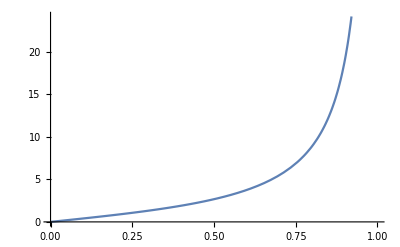

```mathematica
Plot[(4 y)/(1-y^2),{y,0,1}]
```

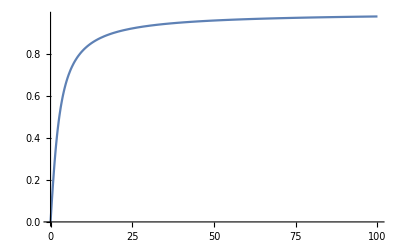

```mathematica
Plot[((8+ν^2-4 √(4+ν^2))/(8+ν^2+4 √(4+ν^2)))^(1/4),{ν,0,100},PlotRange->All]
```

```mathematica
Reduce[y==((8+ν^2-4 √(4+ν^2))/(8+ν^2+4 √(4+ν^2)))^(1/4)&&ν>0&&0<y,ν]//Simplify
```

0<y<1&&ν==-(4 y)/(-1+y^2)

```mathematica
toprightpoly[n+3]-((16+3 ν^2)toprightpoly[n+2]+(-16 ν^2-3 ν^4)  toprightpoly[n+1]+ν^6 toprightpoly[n])/.toprightpoly[n+a_]->λ^a/.toprightpoly[n]->1//Factor
```

(λ-ν^2) (-16 λ+λ^2-2 λ ν^2+ν^4)

```mathematica
Collect[-16 λ+λ^2-2 λ ν^2+ν^4,λ]
```

λ^2+ν^4+λ (-16-2 ν^2)

```mathematica
(Λ^2-ν^2)^2-16 Λ^2//Factor
```

(-4 Λ+Λ^2-ν^2) (4 Λ+Λ^2-ν^2)

```mathematica
(-y+y^(2 n)+y^(2+2 n)+y^(1+4 n))/y==0//Apart//Expand
```

```mathematica
-1+y^(4 n)+y^(-1+2 n)+y^(1+2 n)==0
```

```mathematica
y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1
```

### But this is exactly the poly we had in the θ=1 notebook!

## For topleftpoly:

```mathematica
(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))/.n->1//Simplify
```

16-ν^2

```mathematica
(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))/.n->1
```

```mathematica
(16 (-1+3 y^2-3 y^6+y^8))/((-1+y) (1+y) (1-y^2)^2 (1+y^2))//Factor
```

(16 (-1-y+y^2) (-1+y+y^2))/((-1+y)^2 (1+y)^2)

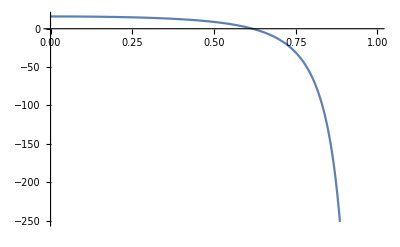

```mathematica
Plot[(16 (-1+3 y^2-3 y^6+y^8))/((-1+y) (1+y) (1-y^2)^2 (1+y^2)),{y,0,1}]
```

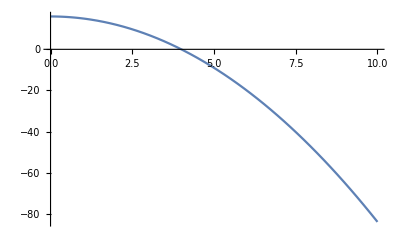

```mathematica
Plot[16-ν^2,{ν,0,10}]
```

```mathematica
16-ν^2/.ν->-(4 y)/(-1+y^2)
```

```mathematica
16-(16 y^2)/((-1+y^2)^2)//Factor
```

(16 (-1-y+y^2) (-1+y+y^2))/((-1+y)^2 (1+y)^2)

```mathematica
Reduce[-1+3 y^2-3 y^6+y^8==0&&0<y<1]//N
```

y==0.618034

```mathematica
Simplify[(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))/.ν->-(4 y)/(-1+y^2),0<y<1]
```

```mathematica
(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/(-1+y^4)//Factor
```

(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))

### Now we got this poly; interestingly, it can always be factored:

```mathematica
(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n))/(-1+y^4)//Apart
```

(y^(2+4 n) (-3+y^2))/((-1+y) (1+y) (1+y^2))+(-1+3 y^2)/((-1+y) (1+y) (1+y^2))

```mathematica
Table[Factor[-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)],{n,0,5}]
```

{(-1+y) (1+y) (1+y^2),(-1+y) (1+y) (1+y^2) (-1-y+y^2) (-1+y+y^2),(-1+y) (1+y) (1+y^2) (1-y-y^2-y^3+y^4) (1+y-y^2+y^3+y^4),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12-3 y^14+y^16),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12-3 y^14+y^16-3 y^18+y^20)}

### After making the sign apparent:

```mathematica
(16^n (1-y^2)^(-2 n) (-(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n))))/((1-y^2) (1+y^2))==(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))//Simplify
```

True

### The sign of the top left and the top right entries of the matrix are the same as the signs of the following two polynomials:

```mathematica
{-(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}//Simplify
```

{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}

```mathematica
Table[{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)},{n,0,10}]
```

{{1-y^4,1+y^2},{1-3 y^2+3 y^6-y^8,-y+y^2+y^4+y^5},{1-3 y^2+3 y^10-y^12,-y+y^4+y^6+y^9},{1-3 y^2+3 y^14-y^16,-y+y^6+y^8+y^13},{1-3 y^2+3 y^18-y^20,-y+y^8+y^10+y^17},{1-3 y^2+3 y^22-y^24,-y+y^10+y^12+y^21},{1-3 y^2+3 y^26-y^28,-y+y^12+y^14+y^25},{1-3 y^2+3 y^30-y^32,-y+y^14+y^16+y^29},{1-3 y^2+3 y^34-y^36,-y+y^16+y^18+y^33},{1-3 y^2+3 y^38-y^40,-y+y^18+y^20+y^37},{1-3 y^2+3 y^42-y^44,-y+y^20+y^22+y^41}}

### So we need to prove that the blue and the yellow polys cannot be simultaneosly positive for any y∈(0,1):

```mathematica
Manipulate[Plot[Evaluate[{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}],{y,0,1},WorkingPrecision->130],{n,1,15,1}]
```

These curves are decreasing in n for any fixed 0<y<1:

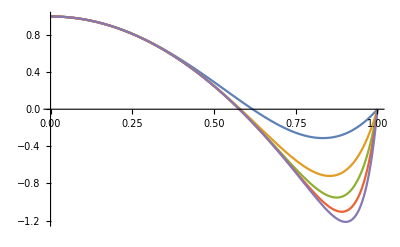

```mathematica
Plot[Evaluate@Table[1-3 y^2+3 y^(2+4 n)-y^(4+4 n),{n,1,5}],{y,0,1}]
```

```mathematica
D[1-3 y^2+3 y^(2+4 n)-y^(4+4 n),n]//Factor
```

-4 y^(2+4 n) (-3+y^2) Log[y]

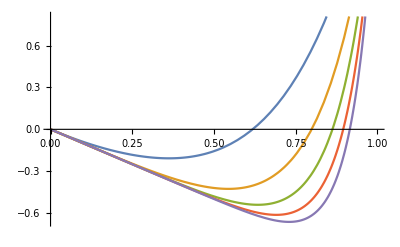

```mathematica
Plot[Evaluate@Table[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),{n,1,5}],{y,0,1}]
```

```mathematica
D[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),n]//Simplify
```

2 y^(2 n) (1+y^2+2 y^(1+2 n)) Log[y]

```mathematica
D[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),y,y]//Simplify
```

y^(2 n) (2 (1+n) (1+2 n)+(2 n (-1+2 n))/y^2+4 n (1+4 n) y^(-1+2 n))

# It seems true that for a general θ∈[0,1], entry_(1,2) and entry_(1,m) have the opposite signs for even values of the matrix size m: CLARIFY the ν vs. (-ν) ISSUE!

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Factor[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,2,8,2}]]
```

{{(4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2),-(2 ν)/(4+θ^2 ν^2)},{(2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2)),ν/(2 (1+θ^2 ν^2)),(θ ν^2)/(2 (1+θ^2 ν^2)),-ν/(2 (1+θ^2 ν^2))},{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(2 ν)/(4+3 θ^2 ν^2),(θ ν^2)/(4+3 θ^2 ν^2),0,(θ ν^2)/(4+3 θ^2 ν^2),-(2 ν)/(4+3 θ^2 ν^2)},{(8-4 θ ν^2+12 θ^2 ν^2-3 θ^3 ν^4+4 θ^4 ν^4)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(ν (4+3 θ^2 ν^2))/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ ν^2)/(4 (1+θ^2 ν^2)),(θ^2 ν^3)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ^3 ν^4)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),-(θ^2 ν^3)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ ν^2)/(4 (1+θ^2 ν^2)),-(ν (4+3 θ^2 ν^2))/(4 (1+θ^2 ν^2) (2+θ^2 ν^2))}}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Factor[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(64-32 θ ν^2+112 θ^2 ν^2-32 θ^3 ν^4+56 θ^4 ν^4-6 θ^5 ν^6+7 θ^6 ν^6)/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2-2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (8+4 θ ν+4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (-8+4 θ ν-4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2+2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)},{(256-128 θ ν^2+576 θ^2 ν^2-192 θ^3 ν^4+432 θ^4 ν^4-80 θ^5 ν^6+120 θ^6 ν^6-8 θ^7 ν^8+9 θ^8 ν^8)/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4-2 θ^5 ν^5+θ^6 ν^6))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^2 ν^3 (4+θ^2 ν^2) (8+6 θ^2 ν^2+θ^3 ν^3))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^3 ν^4 (16-8 θ ν+12 θ^2 ν^2-4 θ^3 ν^3+θ^4 ν^4))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^3 ν^4 (16+8 θ ν+12 θ^2 ν^2+4 θ^3 ν^3+θ^4 ν^4))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^2 ν^3 (4+θ^2 ν^2) (-8-6 θ^2 ν^2+θ^3 ν^3))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4+2 θ^5 ν^5+θ^6 ν^6))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6))}}

```mathematica
Union@Table[RotateLeft[({{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4)}})[[n+1]],n],{n,0,4}]
```

{{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@Factor[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,2,5,1}]]
```

{((4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2) | -(2 ν)/(4+θ^2 ν^2)
(2 ν)/(4+θ^2 ν^2) | (4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2)),((4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (ν (2+θ ν))/(4+3 θ^2 ν^2) | (ν (-2+θ ν))/(4+3 θ^2 ν^2)
(ν (-2+θ ν))/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2) | (ν (2+θ ν))/(4+3 θ^2 ν^2)
(ν (2+θ ν))/(4+3 θ^2 ν^2) | (ν (-2+θ ν))/(4+3 θ^2 ν^2) | (4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2)),((2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2)) | ν/(2 (1+θ^2 ν^2)) | (θ ν^2)/(2 (1+θ^2 ν^2)) | -ν/(2 (1+θ^2 ν^2))
-ν/(2 (1+θ^2 ν^2)) | (2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2)) | ν/(2 (1+θ^2 ν^2)) | (θ ν^2)/(2 (1+θ^2 ν^2))
(θ ν^2)/(2 (1+θ^2 ν^2)) | -ν/(2 (1+θ^2 ν^2)) | (2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2)) | ν/(2 (1+θ^2 ν^2))
ν/(2 (1+θ^2 ν^2)) | (θ ν^2)/(2 (1+θ^2 ν^2)) | -ν/(2 (1+θ^2 ν^2)) | (2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2))),((16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)
(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)
(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)
(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)
(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4) | (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4))}

# General 0<θ≤1, ν>0, and size=odd=m=2k+1; the 1st row of the matrix, multiplied by the determinant (which we already established to be positive)

### Note! In our earlier file central_scheme_positivity.nb, we used a different parametrization: ν here is (–2ν) there. Reason: advection equation rearranged to the other side; the coefficients 1/2 combined into ν – this time we follow a different convention. So in the earlier file the critical matrix element governing non-negativity was at position (1,2), now we have a different position.

```mathematica
Table[((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand,{m,3,9,2}]
```

{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand,{m,3,9,2}]]
```

{{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,ν/2+(θ ν^2)/4,-ν/2+(θ ν^2)/4},{1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,-ν/2-(θ^2 ν^3)/4+(θ^3 ν^4)/16},{1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,-1/8 θ^2 ν^3+(θ^3 ν^4)/16-(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ ν^2)/4+(3 θ^3 ν^4)/16+(θ^4 ν^5)/32+(θ^5 ν^6)/64,-ν/2-(θ^2 ν^3)/2-(3 θ^4 ν^5)/32+(θ^5 ν^6)/64},{1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,ν/2+(3 θ^2 ν^3)/4+(5 θ^4 ν^5)/16+(θ^6 ν^7)/32+(θ^7 ν^8)/256,(θ ν^2)/4+(5 θ^3 ν^4)/16+(3 θ^5 ν^6)/32-(θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ^3 ν^4)/16-(θ^4 ν^5)/32+(3 θ^5 ν^6)/64-(θ^6 ν^7)/64+(θ^7 ν^8)/256,(θ^3 ν^4)/16+(θ^4 ν^5)/32+(3 θ^5 ν^6)/64+(θ^6 ν^7)/64+(θ^7 ν^8)/256,-1/8 θ^2 ν^3-(θ^4 ν^5)/8+(θ^5 ν^6)/64-(3 θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ ν^2)/4+(5 θ^3 ν^4)/16+(3 θ^5 ν^6)/32+(θ^6 ν^7)/128+(θ^7 ν^8)/256,-ν/2-(3 θ^2 ν^3)/4-(5 θ^4 ν^5)/16-(θ^6 ν^7)/32+(θ^7 ν^8)/256}}

### It seems that the top left elements satisfy a second-order recursion, while all the others in the 1st row satistfy the SAME 3rd-order recursion as a function of the odd matirx size

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,11,2}]]
```

{1+(θ^2 ν^2)/2,-1/16 θ^4 ν^4}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,2]]//Simplify//Expand,{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,3]]//Simplify//Expand,{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,4]]//Simplify//Expand,{m,5,17,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,5]]//Simplify//Expand,{m,5,17,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,6]]//Simplify//Expand,{m,7,19,2}]]
```

### Examining the characteristic polynomials of the obtained recursions

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
λ^3-((1+(3 θ^2 ν^2)/4)λ^2+(-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16)λ+((θ^6 ν^6)/64))//Factor
```

1/64 (4 λ-θ^2 ν^2) (-16 λ+16 λ^2-8 θ^2 λ ν^2+θ^4 ν^4)

```mathematica
{1+(θ^2 ν^2)/2,-1/16 θ^4 ν^4}
```

```mathematica
λ^2-((1+(θ^2 ν^2)/2)λ+(-1/16 θ^4 ν^4))//Factor
```

1/16 (-16 λ+16 λ^2-8 θ^2 λ ν^2+θ^4 ν^4)

### Two observations: 1. the new variable μ=(ν θ)^2 seems to be advatageous (we used the same variable when dealing with the determinants!) 2. the char. poly of the 3rd-order recursion contains that of the 2nd-order one as a factor Remark: matrix size=2k+1

### The explicit form of the top left element:

```mathematica
RSolve[{topleftelement[k+2]== (1+μ/2)topleftelement[k+1]-1/16 μ^2  topleftelement[k],topleftelement[1]==1-μ/(2θ)+(3 μ)/4,topleftelement[2]==1-μ/(2θ)+(5 μ)/4-μ^2/(4θ)+(5 μ^2)/16},topleftelement[k],k]//Expand
```

{{topleftelement[k]→2^(-1-2 k) (2+μ-2 √(1+μ))^k-(2^(-1-2 k) (2+μ-2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(θ √(1+μ))+2^(-1-2 k) (2+μ+2 √(1+μ))^k+(2^(-1-2 k) (2+μ+2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(θ √(1+μ))}}

### We apply a non-linear change of variables: μ== (4 y^2)/((1-y^2)^2)∈(0,+∞) ⧦ y==(√(1+μ)-1)/(√μ)==(√(1+(θ ν)^2)-1)/(θ ν)∈(0,1), with μ==(θ ν)^2 Reason: this way μ y^2==2+μ-2 √(1+μ) and μ/y^2==2+μ+2 √(1+μ)

```mathematica
μ ((√(1+μ)-1)/(√μ))^2//Expand//Together
```

2+μ-2 √(1+μ)

```mathematica
μ/((√(1+μ)-1)/(√μ))^2==2+μ+2 √(1+μ)//Simplify
```

True

```mathematica
Reduce[μ== (4 y^2)/((1-y^2)^2)&&μ>0&&0<y<1,y]
```

μ>0&&y==Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]

### ToRadicals here selects the wrong root!

```mathematica
Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]//ToRadicals
```

√(1+2/μ+(2 √(1+μ))/μ)

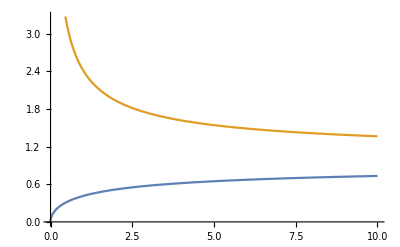

```mathematica
Plot[{Root[μ+(-4-2 μ) #1^2+μ #1^4&,3],√(1+2/μ+(2 √(1+μ))/μ)},{μ,0,10}]
```

that is

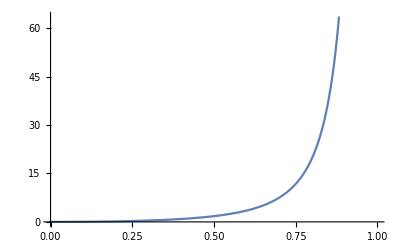

```mathematica
Plot[(4 y^2)/((1-y^2)^2),{y,0,1}]
```

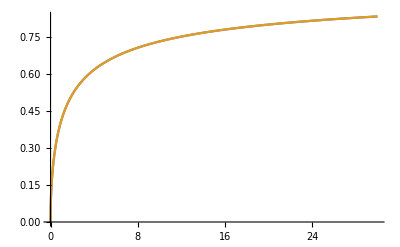

```mathematica
Plot[{(√(1+μ)-1)/(√μ),Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]},{μ,0,30},PlotRange->All]
```

```mathematica
Simplify[2^(-1-2 k) (2+μ-2 √(1+μ))^k-(2^(-1-2 k) (2+μ-2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(θ √(1+μ))+2^(-1-2 k) (2+μ+2 √(1+μ))^k+(2^(-1-2 k) (2+μ+2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(θ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)

```mathematica
FullSimplify[((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)/.y->(√(1+μ)-1)/(√μ)/.μ->(ν θ)^2,ν>0&&0<θ≤1&&k∈Integers]
```

((θ ν)^(4 k) (2-2 √(1+θ^2 ν^2))^(-2 k) (-θ-((-2+θ) (-1+√(1+θ^2 ν^2))^2)/(θ^2 ν^2)+θ ((-1+√(1+θ^2 ν^2))/(θ ν))^(4 (1+k))+(-2+θ) ((-1+√(1+θ^2 ν^2))/(θ ν))^(2+4 k)))/(θ (-1+((-1+√(1+θ^2 ν^2))^4)/(θ^4 ν^4)))

```mathematica
Expand@FullSimplify[Table[((θ ν)^(4 k) (2-2 √(1+θ^2 ν^2))^(-2 k) (-θ-((-2+θ) (-1+√(1+θ^2 ν^2))^2)/(θ^2 ν^2)+θ ((-1+√(1+θ^2 ν^2))/(θ ν))^(4 (1+k))+(-2+θ) ((-1+√(1+θ^2 ν^2))/(θ ν))^(2+4 k)))/(θ (-1+((-1+√(1+θ^2 ν^2))^4)/(θ^4 ν^4))),{k,1,6}],ν>0&&0<θ≤1&&k∈Integers]
```

{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,1-(θ ν^2)/2+(11 θ^2 ν^2)/4-θ^3 ν^4+(11 θ^4 ν^4)/4-(21 θ^5 ν^6)/32+(77 θ^6 ν^6)/64-(5 θ^7 ν^8)/32+(55 θ^8 ν^8)/256-(5 θ^9 ν^10)/512+(11 θ^10 ν^10)/1024,1-(θ ν^2)/2+(13 θ^2 ν^2)/4-(5 θ^3 ν^4)/4+(65 θ^4 ν^4)/16-(9 θ^5 ν^6)/8+(39 θ^6 ν^6)/16-(7 θ^7 ν^8)/16+(91 θ^8 ν^8)/128-(35 θ^9 ν^10)/512+(91 θ^10 ν^10)/1024-(3 θ^11 ν^12)/1024+(13 θ^12 ν^12)/4096}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,13,2}]]
```

{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,1-(θ ν^2)/2+(11 θ^2 ν^2)/4-θ^3 ν^4+(11 θ^4 ν^4)/4-(21 θ^5 ν^6)/32+(77 θ^6 ν^6)/64-(5 θ^7 ν^8)/32+(55 θ^8 ν^8)/256-(5 θ^9 ν^10)/512+(11 θ^10 ν^10)/1024,1-(θ ν^2)/2+(13 θ^2 ν^2)/4-(5 θ^3 ν^4)/4+(65 θ^4 ν^4)/16-(9 θ^5 ν^6)/8+(39 θ^6 ν^6)/16-(7 θ^7 ν^8)/16+(91 θ^8 ν^8)/128-(35 θ^9 ν^10)/512+(91 θ^10 ν^10)/1024-(3 θ^11 ν^12)/1024+(13 θ^12 ν^12)/4096}

```mathematica
With[{θ=2/3},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,13,2}]]
```

{1,1+(2 ν^2)/9-ν^4/81,1+(4 ν^2)/9+(2 ν^4)/81-(2 ν^6)/729,1+(2 ν^2)/3+ν^4/9-ν^8/2187,1+(8 ν^2)/9+(20 ν^4)/81+(14 ν^6)/729-(5 ν^8)/6561-(4 ν^10)/59049,1+(10 ν^2)/9+(35 ν^4)/81+(16 ν^6)/243+(14 ν^8)/6561-(14 ν^10)/59049-(5 ν^12)/531441}

```mathematica
Reduce[#&&ν>0]&/@({1,1+(2 ν^2)/9-ν^4/81,1+(4 ν^2)/9+(2 ν^4)/81-(2 ν^6)/729,1+(2 ν^2)/3+ν^4/9-ν^8/2187,1+(8 ν^2)/9+(20 ν^4)/81+(14 ν^6)/729-(5 ν^8)/6561-(4 ν^10)/59049,1+(10 ν^2)/9+(35 ν^4)/81+(16 ν^6)/243+(14 ν^8)/6561-(14 ν^10)/59049-(5 ν^12)/531441}≥0//Thread)
```

{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}

```mathematica
{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}//N
```

{ν>0.,0.<ν≤4.66132,0.<ν≤4.32475,0.<ν≤4.26183,0.<ν≤4.24734,0.<ν≤4.24381}

### so the sign of the top left element is detemined by the sign of ((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ), which is

y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ

```mathematica
Table[Reduce[(0≤y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->2/3)&&0<y<1],{k,1,6}]
```

{0<y<1,0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20-2 #1^22+#1^24&,3]}

```mathematica
Reduce[#&&ν>0]&/@({0<y<1,0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20-2 #1^22+#1^24&,3]}/.y->(√(1+μ)-1)/(√μ)/.μ->(θ ν)^2/.θ->2/3)//RootReduce
```

```mathematica
{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}//N
```

{ν>0.,0.<ν≤4.66132,0.<ν≤4.32475,0.<ν≤4.26183,0.<ν≤4.24734,0.<ν≤4.24381}

### The explicit form of the element_(1,2):

The initial conditions:

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,2]]//Simplify//Expand,{m,3,13,2}]]
```

{ν/2+(θ ν^2)/4,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64,ν/2+(3 θ^2 ν^3)/4+(5 θ^4 ν^5)/16+(θ^6 ν^7)/32+(θ^7 ν^8)/256,ν/2+θ^2 ν^3+(21 θ^4 ν^5)/32+(5 θ^6 ν^7)/32+(5 θ^8 ν^9)/512+(θ^9 ν^10)/1024,ν/2+(5 θ^2 ν^3)/4+(9 θ^4 ν^5)/8+(7 θ^6 ν^7)/16+(35 θ^8 ν^9)/512+(3 θ^10 ν^11)/1024+(θ^11 ν^12)/4096}

```mathematica
{ν/2+(θ ν^2)/4,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64}/.θ->(√μ)/ν
```

{ν/2+(√μ ν)/4,ν/2+(μ ν)/4+1/16 μ^(3/2) ν,ν/2+(μ ν)/2+(3 μ^2 ν)/32+1/64 μ^(5/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion:

```mathematica
RSolve[{secondelement[k+3]== (1+(3 μ)/4)secondelement[k+2]+(-μ/4-(3 μ^2)/16)secondelement[k+1]+μ^3/64 secondelement[k],secondelement[1]==ν/2+(√μ ν)/4,secondelement[2]==ν/2+(μ ν)/4+1/16 μ^(3/2) ν,secondelement[3]==ν/2+(μ ν)/2+(3 μ^2 ν)/32+1/64 μ^(5/2) ν},secondelement[k],k]//Expand
```

{{secondelement[k]→2^(-2 k) μ^(-1/2+k) ν-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))}}

```mathematica
Simplify[2^(-2 k) μ^(-1/2+k) ν-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y+y^(2 k)+y^(2+2 k)-y^(1+4 k)) ν)/(2 (y+y^3))

### Its sign is determined:

```mathematica
y+y^(2 k)+y^(2+2 k)-y^(1+4 k)
```

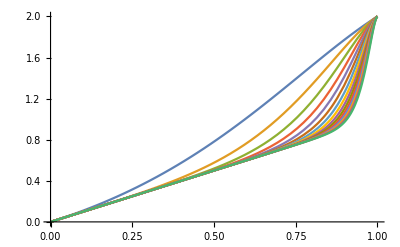

```mathematica
Plot[Evaluate@Table[y+y^(2 k)+y^(2+2 k)-y^(1+4 k),{k,1,15}],{y,0,1}]
```

```mathematica
y^(2+2 k)(1-y^(1+4 k-2k-2))
```

y^(2+2 k) (1-y^(-1+2 k))

which is trivially positive for 0<y<1.

### The explicit form of the element_(1,3):

The initial conditions:

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,3]]//Simplify//Expand,{m,3,7,2}]]
```

{-ν/2+(θ ν^2)/4,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64}

```mathematica
{-ν/2+(θ ν^2)/4,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64}/.θ->(√μ)/ν
```

{-ν/2+(√μ ν)/4,(√μ ν)/4-(μ ν)/8+1/16 μ^(3/2) ν,(√μ ν)/4+3/16 μ^(3/2) ν-(μ^2 ν)/32+1/64 μ^(5/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion:

```mathematica
RSolve[{thirdelement[k+3]== (1+(3 μ)/4)thirdelement[k+2]+(-μ/4-(3 μ^2)/16)thirdelement[k+1]+μ^3/64 thirdelement[k],thirdelement[1]==-ν/2+(√μ ν)/4,thirdelement[2]==(√μ ν)/4-(μ ν)/8+1/16 μ^(3/2) ν,thirdelement[3]==(√μ ν)/4+3/16 μ^(3/2) ν-(μ^2 ν)/32+1/64 μ^(5/2) ν},thirdelement[k],k]//Expand
```

{{thirdelement[k]→-2^(1-2 k) μ^(-1+k) ν+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ)+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ √(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ)-(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ √(1+μ))}}

```mathematica
Simplify[-2^(1-2 k) μ^(-1+k) ν+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ)+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ √(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ)-(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)) ν)/(2 y^2 (1+y^2))

### Its sign is determined:

```mathematica
y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)
```

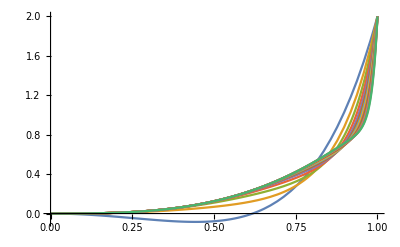

```mathematica
Plot[Evaluate@Table[y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k),{k,1,15}],{y,0,1},PlotRange->All]
```

which is trivially positive for k>1 and 0<y<1.

### The explicit form of the element_(1,4):

The initial conditions: now the matrix size is at least 5

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,4]]//Simplify//Expand,{m,5,9,2}]]
```

{(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256}

```mathematica
{(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256}/.θ->(√μ)/ν
```

{(√μ ν)/4+(μ ν)/8+1/16 μ^(3/2) ν,(μ ν)/8+1/16 μ^(3/2) ν+(μ^2 ν)/16+1/64 μ^(5/2) ν,(μ ν)/8+(μ^2 ν)/8+1/64 μ^(5/2) ν+(3 μ^3 ν)/128+1/256 μ^(7/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion: [NOTE: as for the starting index we need k≥2 to make the matrix size at least 5]

```mathematica
RSolve[{fourthelement[k+3]== (1+(3 μ)/4)fourthelement[k+2]+(-μ/4-(3 μ^2)/16)fourthelement[k+1]+μ^3/64 fourthelement[k],fourthelement[2]==(√μ ν)/4+(μ ν)/8+1/16 μ^(3/2) ν,fourthelement[3]==(μ ν)/8+1/16 μ^(3/2) ν+(μ^2 ν)/16+1/64 μ^(5/2) ν,fourthelement[4]==(μ ν)/8+(μ^2 ν)/8+1/64 μ^(5/2) ν+(3 μ^3 ν)/128+1/256 μ^(7/2) ν},fourthelement[k],k]//Expand
```

{{fourthelement[k]→2^(2-2 k) μ^(-3/2+k) ν+2^(-2 k) μ^(-1/2+k) ν-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/μ-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/(μ √(1+μ))-(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/μ+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))+(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/(μ √(1+μ))}}

```mathematica
Simplify[2^(2-2 k) μ^(-3/2+k) ν+2^(-2 k) μ^(-1/2+k) ν-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/μ-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/(μ √(1+μ))-(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/μ+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))+(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/(μ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)) ν)/(2 y^3 (1+y^2))

### Its sign is determined:

```mathematica
y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)
```

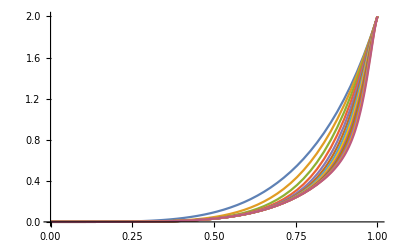

```mathematica
Plot[Evaluate@Table[y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k),{k,2,15}],{y,0,1},PlotRange->All]
```

```mathematica
Reduce[6+2k<1+4k]
```

k>5/2

which is trivially positive for k>2 and 0<y<1. For k=2:

```mathematica
y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)/.k->2
```

y^4+y^5-y^9+y^10

### The consecutive elements in the 1st row (1st, 2nd, 3rd, 4th):

```mathematica
{((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ),-((-1+y^2)^(1-2 k) (y+y^(2 k)+y^(2+2 k)-y^(1+4 k)) ν)/(2 (y+y^3)),-((-1+y^2)^(1-2 k) (y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)) ν)/(2 y^2 (1+y^2)),-((-1+y^2)^(1-2 k) (y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)) ν)/(2 y^3 (1+y^2))}
```

After some transformations:

```mathematica
{((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^2) (1+y^2) θ),((1-y^2)^(1-2 k)  ν)/(2 (y+y^3))(y+y^(2 k)+y^(2+2 k)-y^(1+4 k)),((1-y^2)^(1-2 k)  ν)/(2 y^2 (1+y^2))(y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)),((1-y^2)^(1-2 k)  ν)/(2 y^3 (1+y^2))(y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k))}
```

```mathematica
{((1-y^2)^(-1-2 k)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ))/((1+y^2) θ),((1-y^2)^(1-2 k) (1+y^(-1+2 k)+y^(1+2 k)-y^(4 k)) ν)/(2 (1+y^2)),((1-y^2)^(1-2 k) (y-y^(-2+2 k)+y^(2+2 k)+y^(-1+4 k)) ν)/(2  (1+y^2)),((1-y^2)^(1-2 k) (y^2+y^(-3+2 k)+y^(3+2 k)-y^(-2+4 k)) ν)/(2 (1+y^2))}
```

### So from this we conjecture the general structure: with y==(√(1+(θ ν)^2)-1)/(θ ν), ν>0, 0<θ≤1, matrix size m x m with m==2k+1, k≥1 we have element_(1,1) multiplied by the determinant is

```mathematica
((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ)
```

### element_(1,L) multiplied by the determinant with 2≤L≤2k+1 is

```mathematica
((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)))
```

### Checking these formulae by comparing the 1st row of Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)

```mathematica
Expand@FullSimplify[With[{k=7},Flatten[{((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ),Table[((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))),{L,2,2k+1}]}]/.y->(-1+√(1+θ^2 ν^2))/(θ ν)],0<θ≤1&&0<ν]
```

{-16384/((-1+√(1+θ^2 ν^2))^15)+(8192 θ ν^2)/((-1+√(1+θ^2 ν^2))^15)-(122880 θ^2 ν^2)/((-1+√(1+θ^2 ν^2))^15)+(55296 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^15)-(414720 θ^4 ν^4)/((-1+√(1+θ^2 ν^2))^15)+(166400 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^15)-(832000 θ^6 ν^6)/((-1+√(1+θ^2 ν^2))^15)+(294400 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^15)-(1104000 θ^8 ν^8)/((-1+√(1+θ^2 ν^2))^15)+(340032 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^15)-(1020096 θ^10 ν^10)/((-1+√(1+θ^2 ν^2))^15)+(269192 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^15)-(672980 θ^12 ν^12)/((-1+√(1+θ^2 ν^2))^15)+(149226 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^15)-(319770 θ^14 ν^14)/((-1+√(1+θ^2 ν^2))^15)+(58140 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^15)-(218025 θ^16 ν^16)/(2 (-1+√(1+θ^2 ν^2))^15)+(62985 θ^17 ν^18)/(4 (-1+√(1+θ^2 ν^2))^15)-(104975 θ^18 ν^18)/(4 (-1+√(1+θ^2 ν^2))^15)+(46189 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^15)-(138567 θ^20 ν^20)/(32 (-1+√(1+θ^2 ν^2))^15)+(21879 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15)-(29835 θ^22 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15)+(1547 θ^23 ν^24)/(64 (-1+√(1+θ^2 ν^2))^15)-(7735 θ^24 ν^24)/(256 (-1+√(1+θ^2 ν^2))^15)+(455 θ^25 ν^26)/(512 (-1+√(1+θ^2 ν^2))^15)-(525 θ^26 ν^26)/(512 (-1+√(1+θ^2 ν^2))^15)+(105 θ^27 ν^28)/(8192 (-1+√(1+θ^2 ν^2))^15)-(225 θ^28 ν^28)/(16384 (-1+√(1+θ^2 ν^2))^15)-1/(65536 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+1/(32768 θ √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-1/(65536 θ^2 ν^2 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-(θ^27 ν^28)/(16384 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(θ^28 ν^28)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-(θ^29 ν^30)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(θ^30 ν^30)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(16384 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(√(1+θ^2 ν^2))/(32768 θ (-1+√(1+θ^2 ν^2))^15)+(√(1+θ^2 ν^2))/(65536 θ^2 ν^2 (-1+√(1+θ^2 ν^2))^15)-(268435455 θ ν^2 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(114688 θ^2 ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(1677721601 θ^3 ν^4 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(359424 θ^4 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(4647288831 θ^5 ν^6 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(665600 θ^6 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(7516192769 θ^7 ν^8 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(809600 θ^8 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(7870611455 θ^9 ν^10 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(680064 θ^10 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(5592842241 θ^11 ν^12 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(403788 θ^12 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(2748645375 θ^13 ν^14 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(170544 θ^14 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(934608897 θ^15 ν^16 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(101745 θ^16 ν^16 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^15)-(216408063 θ^17 ν^18 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(20995 θ^18 ν^18 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^15)-(32978945 θ^19 ν^20 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(46189 θ^20 ν^20 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^15)-(3116543 θ^21 ν^22 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(1989 θ^22 ν^22 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15)-(164865 θ^23 ν^24 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(1547 θ^24 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15)-(4031 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(35 θ^26 ν^26 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15)-(27 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(29 θ^28 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15),ν/2+(3 θ^2 ν^3)/2+(55 θ^4 ν^5)/32+(15 θ^6 ν^7)/16+(63 θ^8 ν^9)/256+(7 θ^10 ν^11)/256+(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096-(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^2 ν^3)/8+(5 θ^4 ν^5)/16+(9 θ^6 ν^7)/32+(7 θ^8 ν^9)/64+(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096+(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024-(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096-(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^4 ν^5)/32+(θ^6 ν^7)/16+(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024+(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096+(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256-(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024-(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048-(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^6 ν^7)/128+(θ^7 ν^8)/256+(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024+(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048+(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,-1/128 θ^6 ν^7+(θ^7 ν^8)/256-(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024-(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048-(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256+(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024+(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048+(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-1/32 θ^4 ν^5-(θ^6 ν^7)/16-(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024-(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096-(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024+(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096+(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,-1/8 θ^2 ν^3-(5 θ^4 ν^5)/16-(9 θ^6 ν^7)/32-(7 θ^8 ν^9)/64-(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096-(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096+(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-ν/2-(3 θ^2 ν^3)/2-(55 θ^4 ν^5)/32-(15 θ^6 ν^7)/16-(63 θ^8 ν^9)/256-(7 θ^10 ν^11)/256-(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384}

```mathematica
With[{m=2 7+1},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand]
```

{1-(θ ν^2)/2+(15 θ^2 ν^2)/4-(3 θ^3 ν^4)/2+(45 θ^4 ν^4)/8-(55 θ^5 ν^6)/32+(275 θ^6 ν^6)/64-(15 θ^7 ν^8)/16+(225 θ^8 ν^8)/128-(63 θ^9 ν^10)/256+(189 θ^10 ν^10)/512-(7 θ^11 ν^12)/256+(35 θ^12 ν^12)/1024-(7 θ^13 ν^14)/8192+(15 θ^14 ν^14)/16384,ν/2+(3 θ^2 ν^3)/2+(55 θ^4 ν^5)/32+(15 θ^6 ν^7)/16+(63 θ^8 ν^9)/256+(7 θ^10 ν^11)/256+(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096-(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^2 ν^3)/8+(5 θ^4 ν^5)/16+(9 θ^6 ν^7)/32+(7 θ^8 ν^9)/64+(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096+(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024-(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096-(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^4 ν^5)/32+(θ^6 ν^7)/16+(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024+(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096+(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256-(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024-(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048-(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^6 ν^7)/128+(θ^7 ν^8)/256+(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024+(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048+(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,-1/128 θ^6 ν^7+(θ^7 ν^8)/256-(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024-(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048-(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256+(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024+(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048+(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-1/32 θ^4 ν^5-(θ^6 ν^7)/16-(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024-(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096-(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024+(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096+(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,-1/8 θ^2 ν^3-(5 θ^4 ν^5)/16-(9 θ^6 ν^7)/32-(7 θ^8 ν^9)/64-(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096-(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096+(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-ν/2-(3 θ^2 ν^3)/2-(55 θ^4 ν^5)/32-(15 θ^6 ν^7)/16-(63 θ^8 ν^9)/256-(7 θ^10 ν^11)/256-(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384}

We check it for k=1, 2, ..., 10. The k=10 case is

```mathematica
With[{k=10},Expand@Simplify[Flatten[{((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ),Table[((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))),{L,2,2k+1}]}]/.y->(-1+√(1+θ^2 ν^2))/(θ ν),0<θ≤1&&0<ν]-With[{m=2 k+1},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand]]
```

```mathematica
{-1+(θ ν^2)/2-(21 θ^2 ν^2)/4+(9 θ^3 ν^4)/4-(189 θ^4 ν^4)/16+(17 θ^5 ν^6)/4-(119 θ^6 ν^6)/8+(35 θ^7 ν^8)/8-(735 θ^8 ν^8)/64+(1365 θ^9 ν^10)/512-(5733 θ^10 ν^10)/1024+(1001 θ^11 ν^12)/1024-(7007 θ^12 ν^12)/4096+(429 θ^13 ν^14)/2048-(1287 θ^14 ν^14)/4096+(99 θ^15 ν^16)/4096-(2079 θ^16 ν^16)/65536+(165 θ^17 ν^18)/131072-(385 θ^18 ν^18)/262144+(5 θ^19 ν^20)/262144-(21 θ^20 ν^20)/1048576-47185920/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+2097152/(θ (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-4194304/(θ^2 ν^2 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(22020096 θ ν^2)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(247463936 θ^2 ν^2)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(107347968 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(803405824 θ^4 ν^4)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(322502656 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1808318464 θ^6 ν^6)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(668344320 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2994819072 θ^8 ν^8)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1013354496 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3779973120 θ^10 ν^10)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1163481088 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3716016128 θ^12 ν^12)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1032886272 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2883474176 θ^14 ν^14)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(717704064 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1779070656 θ^16 ν^16)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(392683200 θ^17 ν^18)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(875122560 θ^18 ν^18)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(169344630 θ^19 ν^20)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(342721275 θ^20 ν^20)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(57358665 θ^21 ν^22)/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(425182485 θ^22 ν^22)/(4 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(121090515 θ^23 ν^24)/(8 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(413836815 θ^24 ν^24)/(16 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(49142835 θ^25 ν^26)/(16 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(77893065 θ^26 ν^26)/(16 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(15043725 θ^27 ν^28)/(32 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(44462565 θ^28 ν^28)/(64 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3380195 θ^29 ν^30)/(64 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(74847175 θ^30 ν^30)/(1024 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8580495 θ^31 ν^32)/(2048 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(22328515 θ^32 ν^32)/(4096 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(908523 θ^33 ν^34)/(4096 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(139403 θ^34 ν^34)/(512 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(235543 θ^35 ν^36)/(32768 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(547239 θ^36 ν^36)/(65536 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8085 θ^37 ν^38)/(65536 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(35651 θ^38 ν^38)/(262144 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(55 θ^39 ν^40)/(65536 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(231 θ^40 ν^40)/(262144 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(45088768 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2097152 √(1+θ^2 ν^2))/(θ (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4194304 √(1+θ^2 ν^2))/(θ^2 ν^2 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20971520 θ ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(225443840 θ^2 ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(97124352 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(696057856 θ^4 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(276430848 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1485815808 θ^6 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(541040640 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2326474752 θ^8 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(772079616 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2766618624 θ^10 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(831057920 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2552535040 θ^12 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(688590848 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1850587904 θ^14 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(444292992 θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1061366592 θ^16 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(224390400 θ^17 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(482439360 θ^18 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88704330 θ^19 ν^20 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(173376645 θ^20 ν^20 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(27313650 θ^21 ν^22 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(195747825 θ^22 ν^22 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51895935 θ^23 ν^24 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(171655785 θ^24 ν^24 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2340135 θ^25 ν^26 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14375115 θ^26 ν^26 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5014575 θ^27 ν^28 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14375115 θ^28 ν^28 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(482885 θ^29 ν^30 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(20764055 θ^30 ν^30 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2042975 θ^31 ν^32 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5167525 θ^32 ν^32 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(43263 θ^33 ν^34 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(206701 θ^34 ν^34 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(33649 θ^35 ν^36 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(76153 θ^36 ν^36 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(385 θ^37 ν^38 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3311 θ^38 ν^38 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5 θ^39 ν^40 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^40 ν^40 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^21 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-ν/2-(9 θ^2 ν^3)/4-(17 θ^4 ν^5)/4-(35 θ^6 ν^7)/8-(1365 θ^8 ν^9)/512-(1001 θ^10 ν^11)/1024-(429 θ^12 ν^13)/2048-(99 θ^14 ν^15)/4096-(165 θ^16 ν^17)/131072-(5 θ^18 ν^19)/262144-(θ^19 ν^20)/1048576-524288/(θ^2 ν (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5242880 ν)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(24248320 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(68812800 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(134041600 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189956096 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(202526720 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(165703680 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(105183000 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(52026000 θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^17 ν^18)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20030010 θ^18 ν^19)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11 θ^19 ν^20)/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5965050 θ^20 ν^21)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13 θ^21 ν^22)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21729825 θ^22 ν^23)/(16 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(69 θ^23 ν^24)/(4 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(928625 θ^24 ν^25)/(4 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3605 θ^25 ν^26)/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(928625 θ^26 ν^27)/(32 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3731 θ^27 ν^28)/(512 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(81719 θ^28 ν^29)/(32 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2431 θ^29 ν^30)/(1024 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1225785 θ^30 ν^31)/(8192 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(957 θ^31 ν^32)/(2048 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21945 θ^32 ν^33)/(4096 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3333 θ^33 ν^34)/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3325 θ^34 ν^35)/(32768 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(335 θ^35 ν^36)/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(25 θ^36 ν^37)/(32768 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5 θ^37 ν^38)/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(524288 √(1+θ^2 ν^2))/(θ^2 ν (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4980736 ν √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21823488 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(58490880 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(107233280 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(142467072 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(141768704 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(107707392 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(63109800 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(28614300 θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^17 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(10015005 θ^18 ν^19 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5 θ^19 ν^20 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5368545 θ^20 ν^21 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^21 ν^22 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4345965 θ^22 ν^23 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25 θ^23 ν^24 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1300075 θ^24 ν^25 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2275 θ^25 ν^26 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(557175 θ^26 ν^27 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^27 ν^28 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(81719 θ^28 ν^29 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2145 θ^29 ν^30 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(245157 θ^30 ν^31 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(165 θ^31 ν^32 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(13167 θ^32 ν^33 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(825 θ^33 ν^34 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(665 θ^34 ν^35 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25 θ^35 ν^36 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5 θ^36 ν^37 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^37 ν^38 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-(θ ν^2)/4-(17 θ^3 ν^4)/16-(15 θ^5 ν^6)/8-(455 θ^7 ν^8)/256-(1001 θ^9 ν^10)/1024-(1287 θ^11 ν^12)/4096-(231 θ^13 ν^14)/4096-(165 θ^15 ν^16)/32768-(45 θ^17 ν^18)/262144+(θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+131072/(θ (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1245184 θ ν^2)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5447680 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14553088 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(26537984 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34981888 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34435296 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25786800 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14827410 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(6561555 θ^17 ν^18)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^18 ν^19)/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17809935 θ^19 ν^20)/(8 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(47 θ^20 ν^21)/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9174815 θ^21 ν^22)/(16 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(935 θ^22 ν^23)/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3528775 θ^23 ν^24)/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2821 θ^24 ν^25)/(256 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(988057 θ^25 ν^26)/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5291 θ^26 ν^27)/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1552661 θ^27 ν^28)/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(759 θ^28 ν^29)/(512 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(202521 θ^29 ν^30)/(2048 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2013 θ^30 ν^31)/(8192 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(128877 θ^31 ν^32)/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1365 θ^32 ν^33)/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5415 θ^33 ν^34)/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(181 θ^34 ν^35)/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(361 θ^35 ν^36)/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^36 ν^37)/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^37 ν^38)/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(131072 √(1+θ^2 ν^2))/(θ (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1179648 θ ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4874240 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12255232 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20951040 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(25776128 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(23560992 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(16286400 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8584290 θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3453450 θ^17 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^18 ν^19 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8436285 θ^19 ν^20 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^20 ν^21 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(482885 θ^21 ν^22 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(665 θ^22 ν^23 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1300075 θ^23 ν^24 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1729 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(156009 θ^25 ν^26 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2717 θ^26 ν^27 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(408595 θ^27 ν^28 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(627 θ^28 ν^29 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10659 θ^29 ν^30 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(627 θ^30 ν^31 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20349 θ^31 ν^32 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(285 θ^32 ν^33 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(285 θ^33 ν^34 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^34 ν^35 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^35 ν^36 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/8 θ^2 ν^3-(θ^4 ν^5)/2-(105 θ^6 ν^7)/128-(91 θ^8 ν^9)/128-(715 θ^10 ν^11)/2048-(99 θ^12 ν^13)/1024-(231 θ^14 ν^15)/16384-(15 θ^16 ν^17)/16384-(θ^17 ν^18)/262144-(9 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576-(32768 ν)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(294912 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1216512 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3047424 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5178240 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(6314112 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5700240 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3875040 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3996135 θ^16 ν^17)/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^17 ν^18)/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1562275 θ^18 ν^19)/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3677355 θ^20 ν^21)/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(953 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(200583 θ^22 ν^23)/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2955 θ^23 ν^24)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2028117 θ^24 ν^25)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5823 θ^25 ν^26)/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(223839 θ^26 ν^27)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3641 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(130815 θ^28 ν^29)/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2799 θ^29 ν^30)/(8192 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2907 θ^30 ν^31)/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2457 θ^31 ν^32)/(65536 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8721 θ^32 ν^33)/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(525 θ^33 ν^34)/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(81 θ^34 ν^35)/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(9 θ^35 ν^36)/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(32768 ν √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(278528 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1081344 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2539520 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4027520 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4560192 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3800160 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2368080 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2220075 θ^16 ν^17 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^17 ν^18 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1562275 θ^18 ν^19 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^19 ν^20 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(408595 θ^20 ν^21 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(681 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(156009 θ^22 ν^23 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1833 θ^23 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(676039 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3069 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(124355 θ^26 ν^27 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(99 θ^27 ν^28 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14535 θ^28 ν^29 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(963 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(969 θ^30 ν^31 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(621 θ^31 ν^32 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(969 θ^32 ν^33 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(83 θ^33 ν^34 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9 θ^34 ν^35 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^35 ν^36 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/16 θ^3 ν^4-(15 θ^5 ν^6)/64-(91 θ^7 ν^8)/256-(143 θ^9 ν^10)/512-(495 θ^11 ν^12)/4096-(231 θ^13 ν^14)/8192-(105 θ^15 ν^16)/32768+(θ^16 ν^17)/131072-(9 θ^17 ν^18)/65536+(θ^18 ν^19)/262144-(θ^19 ν^20)/1048576+(8192 θ ν^2)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(69632 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(269824 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(631040 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(993888 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1113840 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(914940 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(559130 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^16 ν^17)/(4 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2042975 θ^17 ν^18)/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^18 ν^19)/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1389223 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^20 ν^21)/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1389223 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2939 θ^22 ν^23)/(256 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(499681 θ^23 ν^24)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(715 θ^24 ν^25)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(499681 θ^25 ν^26)/(1024 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3471 θ^26 ν^27)/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(82365 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(39 θ^28 ν^29)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(16473 θ^29 ν^30)/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1897 θ^30 ν^31)/(65536 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(867 θ^31 ν^32)/(16384 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(147 θ^32 ν^33)/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(289 θ^33 ν^34)/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^34 ν^35)/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^35 ν^36)/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8192 θ ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(65536 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(238080 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(519680 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(760032 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(786240 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(592020 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(328900 θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^16 ν^17 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1081575 θ^17 ν^18 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^18 ν^19 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(81719 θ^19 ν^20 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^20 ν^21 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(572033 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1819 θ^22 ν^23 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88179 θ^23 ν^24 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(187 θ^24 ν^25 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(146965 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1479 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4845 θ^27 ν^28 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(51 θ^28 ν^29 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2907 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(425 θ^30 ν^31 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51 θ^31 ν^32 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17 θ^32 ν^33 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17 θ^33 ν^34 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/32 θ^4 ν^5-(7 θ^6 ν^7)/64-(39 θ^8 ν^9)/256-(55 θ^10 ν^11)/512-(165 θ^12 ν^13)/4096-(63 θ^14 ν^15)/8192-(θ^15 ν^16)/65536-(21 θ^16 ν^17)/32768-(3 θ^17 ν^18)/262144-(θ^18 ν^19)/65536-(θ^19 ν^20)/1048576-(2048 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(16384 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(59392 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(129024 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(187200 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(191360 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(141680 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^15 ν^16)/(4 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(76912 θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^17 ν^18)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(245157 θ^18 ν^19)/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^19 ν^20)/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17765 θ^20 ν^21)/(2 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(29393 θ^22 ν^23)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2867 θ^23 ν^24)/(512 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4199 θ^24 ν^25)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3509 θ^25 ν^26)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12597 θ^26 ν^27)/(512 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(649 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(357 θ^28 ν^29)/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(539 θ^29 ν^30)/(16384 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^30 ν^31)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(55 θ^31 ν^32)/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^32 ν^33)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^33 ν^34)/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2048 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(15360 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(51968 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(104832 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(140400 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(131560 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(88550 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^15 ν^16 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(43263 θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^17 ν^18 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(245157 θ^18 ν^19 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^19 ν^20 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(124355 θ^20 ν^21 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(88179 θ^22 ν^23 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(751 θ^23 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(20995 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(753 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(109 θ^27 ν^28 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1071 θ^28 ν^29 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(265 θ^29 ν^30 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^30 ν^31 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(35 θ^31 ν^32 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^32 ν^33 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^33 ν^34 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/64 θ^5 ν^6-(13 θ^7 ν^8)/256-(33 θ^9 ν^10)/512-(165 θ^11 ν^12)/4096-(105 θ^13 ν^14)/8192+(θ^14 ν^15)/32768-(63 θ^15 ν^16)/32768+(θ^16 ν^17)/32768-(7 θ^17 ν^18)/65536+(3 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(512 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3840 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12960 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(26000 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34500 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(31878 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^14 ν^15)/(4 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(168245 θ^15 ν^16)/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^16 ν^17)/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(159885 θ^17 ν^18)/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^18 ν^19)/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(218025 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^20 ν^21)/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(104975 θ^21 ν^22)/(128 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^22 ν^23)/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(138567 θ^23 ν^24)/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3503 θ^24 ν^25)/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(29835 θ^25 ν^26)/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5139 θ^26 ν^27)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7735 θ^27 ν^28)/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(513 θ^28 ν^29)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(525 θ^29 ν^30)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(355 θ^30 ν^31)/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(225 θ^31 ν^32)/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3 θ^32 ν^33)/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^33 ν^34)/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(512 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3584 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11232 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20800 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(25300 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21252 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^14 ν^15 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(100947 θ^15 ν^16 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^16 ν^17 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10659 θ^17 ν^18 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^18 ν^19 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(101745 θ^19 ν^20 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^20 ν^21 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20995 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^22 ν^23 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(46189 θ^23 ν^24 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1501 θ^24 ν^25 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1989 θ^25 ν^26 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1709 θ^26 ν^27 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1547 θ^27 ν^28 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(15 θ^28 ν^29 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(35 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(45 θ^30 ν^31 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(15 θ^31 ν^32 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/128 θ^6 ν^7-(3 θ^8 ν^9)/128-(55 θ^10 ν^11)/2048-(15 θ^12 ν^13)/1024-(θ^13 ν^14)/16384-(63 θ^14 ν^15)/16384-(5 θ^15 ν^16)/65536-(7 θ^16 ν^17)/16384-(3 θ^17 ν^18)/131072-(7 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576-(128 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(896 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2800 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5152 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12397 θ^12 ν^13)/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^13 ν^14)/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10241 θ^14 ν^15)/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^15 ν^16)/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(47481 θ^16 ν^17)/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^17 ν^18)/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4845 θ^18 ν^19)/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88179 θ^20 ν^21)/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^21 ν^22)/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17017 θ^22 ν^23)/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^23 ν^24)/(4096 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17017 θ^24 ν^25)/(2048 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5149 θ^25 ν^26)/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(637 θ^26 ν^27)/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1043 θ^27 ν^28)/(32768 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3185 θ^28 ν^29)/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(399 θ^29 ν^30)/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(49 θ^30 ν^31)/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7 θ^31 ν^32)/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(128 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(832 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2400 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4048 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8855 θ^12 ν^13 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^13 ν^14 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(13167 θ^14 ν^15 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^15 ν^16 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(6783 θ^16 ν^17 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^17 ν^18 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4845 θ^18 ν^19 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^19 ν^20 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(37791 θ^20 ν^21 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12155 θ^22 ν^23 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^23 ν^24 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2431 θ^24 ν^25 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1717 θ^25 ν^26 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(273 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(125 θ^27 ν^28 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^28 ν^29 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(61 θ^29 ν^30 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7 θ^30 ν^31 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^31 ν^32 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/256 θ^7 ν^8-(11 θ^9 ν^10)/1024-(45 θ^11 ν^12)/4096+(θ^12 ν^13)/8192-(21 θ^13 ν^14)/4096+(3 θ^14 ν^15)/16384-(35 θ^15 ν^16)/32768+(5 θ^16 ν^17)/65536-(21 θ^17 ν^18)/262144+(θ^18 ν^19)/131072-(θ^19 ν^20)/1048576+(32 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(208 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(598 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^12 ν^13)/(4 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8645 θ^13 ν^14)/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^14 ν^15)/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^15 ν^16)/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^16 ν^17)/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^17 ν^18)/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^18 ν^19)/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8619 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^20 ν^21)/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(31603 θ^21 ν^22)/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^22 ν^23)/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9295 θ^23 ν^24)/(2048 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^24 ν^25)/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(13013 θ^25 ν^26)/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1039 θ^26 ν^27)/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1183 θ^27 ν^28)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(95 θ^28 ν^29)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(169 θ^29 ν^30)/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^30 ν^31)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^31 ν^32)/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(32 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(192 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(506 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(770 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^12 ν^13 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5985 θ^13 ν^14 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^14 ν^15 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(969 θ^15 ν^16 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^16 ν^17 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(6783 θ^17 ν^18 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^18 ν^19 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1989 θ^19 ν^20 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^20 ν^21 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12155 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^22 ν^23 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(715 θ^23 ν^24 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^24 ν^25 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(247 θ^26 ν^27 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(91 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(13 θ^28 ν^29 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13 θ^29 ν^30 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/512 θ^8 ν^9-(5 θ^10 ν^11)/1024-(θ^11 ν^12)/4096-(9 θ^12 ν^13)/2048-(7 θ^13 ν^14)/16384-(7 θ^14 ν^15)/4096-(15 θ^15 ν^16)/65536-(35 θ^16 ν^17)/131072-(5 θ^17 ν^18)/131072-(3 θ^18 ν^19)/262144-(θ^19 ν^20)/1048576-(8 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(48 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(126 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^11 ν^12)/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(190 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^13 ν^14)/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2907 θ^14 ν^15)/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^15 ν^16)/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(459 θ^16 ν^17)/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^17 ν^18)/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1547 θ^18 ν^19)/(32 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^19 ν^20)/(1024 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^20 ν^21)/(32 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^21 ν^22)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19305 θ^22 ν^23)/(8192 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^23 ν^24)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1001 θ^24 ν^25)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2079 θ^25 ν^26)/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^26 ν^27)/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(193 θ^27 ν^28)/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(9 θ^28 ν^29)/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3 θ^29 ν^30)/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(44 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(105 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^11 ν^12 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(285 θ^12 ν^13 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^13 ν^14 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(969 θ^14 ν^15 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^15 ν^16 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1071 θ^16 ν^17 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^17 ν^18 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1547 θ^18 ν^19 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^19 ν^20 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(715 θ^20 ν^21 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^21 ν^22 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(6435 θ^22 ν^23 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^23 ν^24 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^24 ν^25 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(495 θ^25 ν^26 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(143 θ^26 ν^27 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3 θ^28 ν^29 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^29 ν^30 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-(θ^9 ν^10)/1024+(θ^10 ν^11)/2048-(9 θ^11 ν^12)/4096+(θ^12 ν^13)/1024-(7 θ^13 ν^14)/4096+(21 θ^14 ν^15)/32768-(35 θ^15 ν^16)/65536+(5 θ^16 ν^17)/32768-(15 θ^17 ν^18)/262144+(5 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(2 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(11 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^10 ν^11)/(4 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(209 θ^11 ν^12)/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^12 ν^13)/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(561 θ^13 ν^14)/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^14 ν^15)/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(935 θ^15 ν^16)/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^16 ν^17)/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^17 ν^18)/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^18 ν^19)/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(11011 θ^19 ν^20)/(2048 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^20 ν^21)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4719 θ^21 ν^22)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^22 ν^23)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4719 θ^23 ν^24)/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2079 θ^24 ν^25)/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(605 θ^25 ν^26)/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(385 θ^26 ν^27)/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(121 θ^27 ν^28)/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5 θ^28 ν^29)/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^29 ν^30)/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^10 ν^11 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(171 θ^11 ν^12 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^12 ν^13 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51 θ^13 ν^14 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^14 ν^15 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(595 θ^15 ν^16 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^16 ν^17 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(273 θ^17 ν^18 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^18 ν^19 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5005 θ^19 ν^20 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^20 ν^21 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^22 ν^23 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^23 ν^24 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(495 θ^24 ν^25 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(55 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(55 θ^26 ν^27 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11 θ^27 ν^28 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-(θ^9 ν^10)/1024-(θ^10 ν^11)/2048-(9 θ^11 ν^12)/4096-(θ^12 ν^13)/1024-(7 θ^13 ν^14)/4096-(21 θ^14 ν^15)/32768-(35 θ^15 ν^16)/65536-(5 θ^16 ν^17)/32768-(15 θ^17 ν^18)/262144-(5 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(2 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(11 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^10 ν^11)/(4 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(209 θ^11 ν^12)/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(189 θ^12 ν^13)/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(561 θ^13 ν^14)/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(119 θ^14 ν^15)/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(935 θ^15 ν^16)/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(735 θ^16 ν^17)/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^17 ν^18)/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5733 θ^18 ν^19)/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(11011 θ^19 ν^20)/(2048 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7007 θ^20 ν^21)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4719 θ^21 ν^22)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1287 θ^22 ν^23)/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4719 θ^23 ν^24)/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2079 θ^24 ν^25)/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(605 θ^25 ν^26)/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(385 θ^26 ν^27)/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(121 θ^27 ν^28)/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5 θ^28 ν^29)/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^29 ν^30)/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^10 ν^11 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(171 θ^11 ν^12 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(153 θ^12 ν^13 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51 θ^13 ν^14 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^14 ν^15 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(595 θ^15 ν^16 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(455 θ^16 ν^17 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(273 θ^17 ν^18 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^18 ν^19 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5005 θ^19 ν^20 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^20 ν^21 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^22 ν^23 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^23 ν^24 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(495 θ^24 ν^25 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(55 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(55 θ^26 ν^27 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11 θ^27 ν^28 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^10 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),(θ^8 ν^9)/512+(5 θ^10 ν^11)/1024-(θ^11 ν^12)/4096+(9 θ^12 ν^13)/2048-(7 θ^13 ν^14)/16384+(7 θ^14 ν^15)/4096-(15 θ^15 ν^16)/65536+(35 θ^16 ν^17)/131072-(5 θ^17 ν^18)/131072+(3 θ^18 ν^19)/262144-(θ^19 ν^20)/1048576+(8 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(48 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(126 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^11 ν^12)/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(190 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^13 ν^14)/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2907 θ^14 ν^15)/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^15 ν^16)/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(459 θ^16 ν^17)/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^17 ν^18)/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1547 θ^18 ν^19)/(32 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^19 ν^20)/(1024 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^20 ν^21)/(32 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^21 ν^22)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19305 θ^22 ν^23)/(8192 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1287 θ^23 ν^24)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^24 ν^25)/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2079 θ^25 ν^26)/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^26 ν^27)/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(193 θ^27 ν^28)/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9 θ^28 ν^29)/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3 θ^29 ν^30)/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(44 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(105 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^11 ν^12 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(285 θ^12 ν^13 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^13 ν^14 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(969 θ^14 ν^15 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^15 ν^16 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1071 θ^16 ν^17 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^17 ν^18 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1547 θ^18 ν^19 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^19 ν^20 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(715 θ^20 ν^21 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^21 ν^22 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(6435 θ^22 ν^23 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(429 θ^23 ν^24 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1001 θ^24 ν^25 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(495 θ^25 ν^26 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(143 θ^26 ν^27 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3 θ^28 ν^29 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^29 ν^30 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^11 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/256 θ^7 ν^8-(11 θ^9 ν^10)/1024-(45 θ^11 ν^12)/4096-(θ^12 ν^13)/8192-(21 θ^13 ν^14)/4096-(3 θ^14 ν^15)/16384-(35 θ^15 ν^16)/32768-(5 θ^16 ν^17)/65536-(21 θ^17 ν^18)/262144-(θ^18 ν^19)/131072-(θ^19 ν^20)/1048576+(32 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(208 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(598 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^12 ν^13)/(4 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8645 θ^13 ν^14)/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(189 θ^14 ν^15)/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^15 ν^16)/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(119 θ^16 ν^17)/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^17 ν^18)/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(735 θ^18 ν^19)/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8619 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5733 θ^20 ν^21)/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(31603 θ^21 ν^22)/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7007 θ^22 ν^23)/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9295 θ^23 ν^24)/(2048 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1287 θ^24 ν^25)/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(13013 θ^25 ν^26)/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1039 θ^26 ν^27)/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1183 θ^27 ν^28)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(95 θ^28 ν^29)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(169 θ^29 ν^30)/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^30 ν^31)/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^31 ν^32)/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(32 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(192 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(506 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(770 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^12 ν^13 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5985 θ^13 ν^14 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(153 θ^14 ν^15 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(969 θ^15 ν^16 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^16 ν^17 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(6783 θ^17 ν^18 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(455 θ^18 ν^19 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1989 θ^19 ν^20 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^20 ν^21 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12155 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^22 ν^23 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(715 θ^23 ν^24 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(429 θ^24 ν^25 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(247 θ^26 ν^27 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(91 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13 θ^28 ν^29 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13 θ^29 ν^30 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^12 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),(θ^6 ν^7)/128+(3 θ^8 ν^9)/128+(55 θ^10 ν^11)/2048+(15 θ^12 ν^13)/1024-(θ^13 ν^14)/16384+(63 θ^14 ν^15)/16384-(5 θ^15 ν^16)/65536+(7 θ^16 ν^17)/16384-(3 θ^17 ν^18)/131072+(7 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(128 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(896 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2800 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5152 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12397 θ^12 ν^13)/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^13 ν^14)/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(10241 θ^14 ν^15)/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^15 ν^16)/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(47481 θ^16 ν^17)/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^17 ν^18)/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4845 θ^18 ν^19)/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(88179 θ^20 ν^21)/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5733 θ^21 ν^22)/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17017 θ^22 ν^23)/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7007 θ^23 ν^24)/(4096 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17017 θ^24 ν^25)/(2048 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5149 θ^25 ν^26)/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(637 θ^26 ν^27)/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1043 θ^27 ν^28)/(32768 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3185 θ^28 ν^29)/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(399 θ^29 ν^30)/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(49 θ^30 ν^31)/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7 θ^31 ν^32)/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(128 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(832 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2400 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4048 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8855 θ^12 ν^13 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^13 ν^14 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13167 θ^14 ν^15 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^15 ν^16 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(6783 θ^16 ν^17 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^17 ν^18 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4845 θ^18 ν^19 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^19 ν^20 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(37791 θ^20 ν^21 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^21 ν^22 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12155 θ^22 ν^23 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3003 θ^23 ν^24 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2431 θ^24 ν^25 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1717 θ^25 ν^26 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(273 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(125 θ^27 ν^28 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(455 θ^28 ν^29 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(61 θ^29 ν^30 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(7 θ^30 ν^31 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^31 ν^32 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^13 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/64 θ^5 ν^6-(13 θ^7 ν^8)/256-(33 θ^9 ν^10)/512-(165 θ^11 ν^12)/4096-(105 θ^13 ν^14)/8192-(θ^14 ν^15)/32768-(63 θ^15 ν^16)/32768-(θ^16 ν^17)/32768-(7 θ^17 ν^18)/65536-(3 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(512 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3840 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12960 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(26000 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34500 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(31878 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^14 ν^15)/(4 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(168245 θ^15 ν^16)/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(189 θ^16 ν^17)/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(159885 θ^17 ν^18)/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(119 θ^18 ν^19)/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(218025 θ^19 ν^20)/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(735 θ^20 ν^21)/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(104975 θ^21 ν^22)/(128 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5733 θ^22 ν^23)/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(138567 θ^23 ν^24)/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3503 θ^24 ν^25)/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(29835 θ^25 ν^26)/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5139 θ^26 ν^27)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(7735 θ^27 ν^28)/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(513 θ^28 ν^29)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(525 θ^29 ν^30)/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(355 θ^30 ν^31)/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(225 θ^31 ν^32)/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3 θ^32 ν^33)/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^33 ν^34)/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(512 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3584 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11232 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20800 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(25300 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21252 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^14 ν^15 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(100947 θ^15 ν^16 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(153 θ^16 ν^17 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10659 θ^17 ν^18 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^18 ν^19 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(101745 θ^19 ν^20 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(455 θ^20 ν^21 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20995 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3003 θ^22 ν^23 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(46189 θ^23 ν^24 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1501 θ^24 ν^25 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1989 θ^25 ν^26 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1709 θ^26 ν^27 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1547 θ^27 ν^28 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(15 θ^28 ν^29 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(35 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(45 θ^30 ν^31 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(15 θ^31 ν^32 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^14 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),(θ^4 ν^5)/32+(7 θ^6 ν^7)/64+(39 θ^8 ν^9)/256+(55 θ^10 ν^11)/512+(165 θ^12 ν^13)/4096+(63 θ^14 ν^15)/8192-(θ^15 ν^16)/65536+(21 θ^16 ν^17)/32768-(3 θ^17 ν^18)/262144+(θ^18 ν^19)/65536-(θ^19 ν^20)/1048576+(2048 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(16384 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(59392 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(129024 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(187200 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(191360 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(141680 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^15 ν^16)/(4 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(76912 θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^17 ν^18)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(245157 θ^18 ν^19)/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(119 θ^19 ν^20)/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17765 θ^20 ν^21)/(2 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(735 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(29393 θ^22 ν^23)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2867 θ^23 ν^24)/(512 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(4199 θ^24 ν^25)/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3509 θ^25 ν^26)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(12597 θ^26 ν^27)/(512 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(649 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(357 θ^28 ν^29)/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(539 θ^29 ν^30)/(16384 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^30 ν^31)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(55 θ^31 ν^32)/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^32 ν^33)/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^33 ν^34)/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2048 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(15360 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51968 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(104832 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(140400 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(131560 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88550 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^15 ν^16 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(43263 θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^17 ν^18 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(245157 θ^18 ν^19 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^19 ν^20 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(124355 θ^20 ν^21 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(455 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88179 θ^22 ν^23 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(751 θ^23 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20995 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(753 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12597 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(109 θ^27 ν^28 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1071 θ^28 ν^29 √(1+θ^2 ν^2))/(4096 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(265 θ^29 ν^30 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^30 ν^31 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(35 θ^31 ν^32 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^32 ν^33 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^33 ν^34 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^15 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-1/16 θ^3 ν^4-(15 θ^5 ν^6)/64-(91 θ^7 ν^8)/256-(143 θ^9 ν^10)/512-(495 θ^11 ν^12)/4096-(231 θ^13 ν^14)/8192-(105 θ^15 ν^16)/32768-(θ^16 ν^17)/131072-(9 θ^17 ν^18)/65536-(θ^18 ν^19)/262144-(θ^19 ν^20)/1048576+(8192 θ ν^2)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(69632 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(269824 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(631040 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(993888 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1113840 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(914940 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(559130 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^16 ν^17)/(4 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2042975 θ^17 ν^18)/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(189 θ^18 ν^19)/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1389223 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(119 θ^20 ν^21)/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1389223 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2939 θ^22 ν^23)/(256 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(499681 θ^23 ν^24)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(715 θ^24 ν^25)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(499681 θ^25 ν^26)/(1024 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3471 θ^26 ν^27)/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(82365 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(39 θ^28 ν^29)/(128 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(16473 θ^29 ν^30)/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1897 θ^30 ν^31)/(65536 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(867 θ^31 ν^32)/(16384 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(147 θ^32 ν^33)/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(289 θ^33 ν^34)/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^34 ν^35)/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^35 ν^36)/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8192 θ ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(65536 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(238080 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(519680 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(760032 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(786240 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(592020 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(328900 θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^16 ν^17 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1081575 θ^17 ν^18 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(153 θ^18 ν^19 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(81719 θ^19 ν^20 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(85 θ^20 ν^21 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(572033 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1819 θ^22 ν^23 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(88179 θ^23 ν^24 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(187 θ^24 ν^25 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(146965 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1479 θ^26 ν^27 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4845 θ^27 ν^28 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51 θ^28 ν^29 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2907 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(425 θ^30 ν^31 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(51 θ^31 ν^32 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17 θ^32 ν^33 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(17 θ^33 ν^34 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^16 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),(θ^2 ν^3)/8+(θ^4 ν^5)/2+(105 θ^6 ν^7)/128+(91 θ^8 ν^9)/128+(715 θ^10 ν^11)/2048+(99 θ^12 ν^13)/1024+(231 θ^14 ν^15)/16384+(15 θ^16 ν^17)/16384-(θ^17 ν^18)/262144+(9 θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+(32768 ν)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(294912 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1216512 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3047424 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5178240 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(6314112 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5700240 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3875040 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3996135 θ^16 ν^17)/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21 θ^17 ν^18)/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1562275 θ^18 ν^19)/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(189 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3677355 θ^20 ν^21)/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(953 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(200583 θ^22 ν^23)/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2955 θ^23 ν^24)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2028117 θ^24 ν^25)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5823 θ^25 ν^26)/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(223839 θ^26 ν^27)/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3641 θ^27 ν^28)/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(130815 θ^28 ν^29)/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2799 θ^29 ν^30)/(8192 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2907 θ^30 ν^31)/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2457 θ^31 ν^32)/(65536 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(8721 θ^32 ν^33)/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(525 θ^33 ν^34)/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(81 θ^34 ν^35)/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(9 θ^35 ν^36)/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(32768 ν √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(278528 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1081344 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2539520 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4027520 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4560192 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3800160 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2368080 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2220075 θ^16 ν^17 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(19 θ^17 ν^18 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1562275 θ^18 ν^19 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(153 θ^19 ν^20 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(408595 θ^20 ν^21 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(681 θ^21 ν^22 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(156009 θ^22 ν^23 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1833 θ^23 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(676039 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3069 θ^25 ν^26 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(124355 θ^26 ν^27 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(99 θ^27 ν^28 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(14535 θ^28 ν^29 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(963 θ^29 ν^30 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(969 θ^30 ν^31 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(621 θ^31 ν^32 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(969 θ^32 ν^33 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(83 θ^33 ν^34 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(9 θ^34 ν^35 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^35 ν^36 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^17 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),-(θ ν^2)/4-(17 θ^3 ν^4)/16-(15 θ^5 ν^6)/8-(455 θ^7 ν^8)/256-(1001 θ^9 ν^10)/1024-(1287 θ^11 ν^12)/4096-(231 θ^13 ν^14)/4096-(165 θ^15 ν^16)/32768-(45 θ^17 ν^18)/262144-(θ^18 ν^19)/524288-(θ^19 ν^20)/1048576+131072/(θ (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1245184 θ ν^2)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5447680 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14553088 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(26537984 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34981888 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(34435296 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25786800 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(14827410 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(6561555 θ^17 ν^18)/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21 θ^18 ν^19)/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(17809935 θ^19 ν^20)/(8 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(47 θ^20 ν^21)/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(9174815 θ^21 ν^22)/(16 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(935 θ^22 ν^23)/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3528775 θ^23 ν^24)/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2821 θ^24 ν^25)/(256 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(988057 θ^25 ν^26)/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5291 θ^26 ν^27)/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1552661 θ^27 ν^28)/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(759 θ^28 ν^29)/(512 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(202521 θ^29 ν^30)/(2048 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2013 θ^30 ν^31)/(8192 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(128877 θ^31 ν^32)/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1365 θ^32 ν^33)/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5415 θ^33 ν^34)/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(181 θ^34 ν^35)/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(361 θ^35 ν^36)/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^36 ν^37)/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^37 ν^38)/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(131072 √(1+θ^2 ν^2))/(θ (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1179648 θ ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4874240 θ^3 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(12255232 θ^5 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20951040 θ^7 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(25776128 θ^9 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(23560992 θ^11 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(16286400 θ^13 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8584290 θ^15 ν^16 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3453450 θ^17 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^18 ν^19 √(1+θ^2 ν^2))/(4 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(8436285 θ^19 ν^20 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^20 ν^21 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(482885 θ^21 ν^22 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(665 θ^22 ν^23 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1300075 θ^23 ν^24 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1729 θ^24 ν^25 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(156009 θ^25 ν^26 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2717 θ^26 ν^27 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(408595 θ^27 ν^28 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(627 θ^28 ν^29 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10659 θ^29 ν^30 √(1+θ^2 ν^2))/(512 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(627 θ^30 ν^31 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(20349 θ^31 ν^32 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(285 θ^32 ν^33 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(285 θ^33 ν^34 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^34 ν^35 √(1+θ^2 ν^2))/(262144 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(19 θ^35 ν^36 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^18 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2))),ν/2+(9 θ^2 ν^3)/4+(17 θ^4 ν^5)/4+(35 θ^6 ν^7)/8+(1365 θ^8 ν^9)/512+(1001 θ^10 ν^11)/1024+(429 θ^12 ν^13)/2048+(99 θ^14 ν^15)/4096+(165 θ^16 ν^17)/131072+(5 θ^18 ν^19)/262144-(θ^19 ν^20)/1048576+524288/(θ^2 ν (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5242880 ν)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(24248320 θ^2 ν^3)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(68812800 θ^4 ν^5)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(134041600 θ^6 ν^7)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(189956096 θ^8 ν^9)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(202526720 θ^10 ν^11)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(165703680 θ^12 ν^13)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(105183000 θ^14 ν^15)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(52026000 θ^16 ν^17)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(θ^17 ν^18)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(20030010 θ^18 ν^19)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(11 θ^19 ν^20)/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5965050 θ^20 ν^21)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13 θ^21 ν^22)/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21729825 θ^22 ν^23)/(16 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(69 θ^23 ν^24)/(4 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(928625 θ^24 ν^25)/(4 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3605 θ^25 ν^26)/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(928625 θ^26 ν^27)/(32 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3731 θ^27 ν^28)/(512 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(81719 θ^28 ν^29)/(32 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(2431 θ^29 ν^30)/(1024 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1225785 θ^30 ν^31)/(8192 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(957 θ^31 ν^32)/(2048 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(21945 θ^32 ν^33)/(4096 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(3333 θ^33 ν^34)/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(3325 θ^34 ν^35)/(32768 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(335 θ^35 ν^36)/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25 θ^36 ν^37)/(32768 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5 θ^37 ν^38)/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(524288 √(1+θ^2 ν^2))/(θ^2 ν (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4980736 ν √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(21823488 θ^2 ν^3 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(58490880 θ^4 ν^5 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(107233280 θ^6 ν^7 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(142467072 θ^8 ν^9 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(141768704 θ^10 ν^11 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(107707392 θ^12 ν^13 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(63109800 θ^14 ν^15 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(28614300 θ^16 ν^17 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^17 ν^18 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(10015005 θ^18 ν^19 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(5 θ^19 ν^20 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5368545 θ^20 ν^21 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(85 θ^21 ν^22 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(4345965 θ^22 ν^23 √(1+θ^2 ν^2))/(8 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25 θ^23 ν^24 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(1300075 θ^24 ν^25 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2275 θ^25 ν^26 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(557175 θ^26 ν^27 √(1+θ^2 ν^2))/(64 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(1001 θ^27 ν^28 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(81719 θ^28 ν^29 √(1+θ^2 ν^2))/(128 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(2145 θ^29 ν^30 √(1+θ^2 ν^2))/(2048 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(245157 θ^30 ν^31 √(1+θ^2 ν^2))/(8192 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(165 θ^31 ν^32 √(1+θ^2 ν^2))/(1024 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(13167 θ^32 ν^33 √(1+θ^2 ν^2))/(16384 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(825 θ^33 ν^34 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(665 θ^34 ν^35 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(25 θ^35 ν^36 √(1+θ^2 ν^2))/(65536 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))-(5 θ^36 ν^37 √(1+θ^2 ν^2))/(131072 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))+(θ^37 ν^38 √(1+θ^2 ν^2))/(524288 (-1+√(1+θ^2 ν^2))^19 (2+(2-2 √(1+θ^2 ν^2))/(θ^2 ν^2)))}//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}